# Retrospective evaluation of school-related measures on pre-vaccination dynamics of SARS-CoV-2

## Canfora B., Escosio R. A., Boldea O., van Dorp C. H., Nunes A., and Rozhnova G.

## Memory and global parameters

```mathematica
(* Clear *)
$HistoryLength=0;
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
Off[General::munfl]
memory:=Row[{"Memory Used:",MemoryInUse[]/1024^2.," MB"}]
SetDirectory[NotebookDirectory[]];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

### PACKAGES AND PARAMETERS

```mathematica
(* External packages *)
AppendTo[$Path,"../packages"];
Needs["plottingFunctions`"];

(*ResourceFunction["DarkMode"][False]*)
(*ResourceFunction["GraphicsBrace"];*)


(* Notebook parameters *)
ifShowFigs = True;
ifExportData = False;
ifExportFigs = False;
exportFormat={".pdf",".eps"};

importExportScenarioResults[labelPrefix_,dataFunction_, subFolder_]:=
Table[Module[{filePath,state},
filePath=FileNameJoin[{"../results"},StringJoin["/",subFolder,"/",labelPrefix,"_",scenarios[[i]],".wxf"]];
If[FileExistsQ[filePath],
state=Import[filePath,"WXF"];
state,
state=dataFunction[i];
Export[filePath,state,"WXF","CompressionLevel"->5];
state]],
{i,1,Length[scenarios]}];

exportFigs[figs_, filename_] := If[ifExportFigs,Table[Export[StringJoin["../figures/",filename, ToString[j],exportFormat⟦i⟧],figs⟦j⟧],{i,1,Length[exportFormat]},{j,1,Length[figs]}]];


(* Known constants *)
(* Age groups *)
numAgeGroups = 10;
listAgeGroups= Table[k, {k, 1, numAgeGroups}];
listChildren = Range[1,3];
listAdults = Range[4,10];
groupIndex = {listChildren, listAdults};

(* Samples *)
numAllSamples = 2000;
stepSamples=20; (* 20 corresponds to 100 samples *)
listSamples=Table[i,{i,1,numAllSamples,stepSamples}];
numSamples = Length[listSamples];

(* Variables *)
numVariables=5;
varNumbers= Table[j, {j, 1, numVariables}];
eqNumbers=Table[k,{k,1,numAgeGroups numVariables}];

(* Scenarios *)
(*scenarios={"Baseline", "Scenario1", "Scenario2", "Scenario1_RelaxedNS", "Scenario1_ZetaSchool","Scenario2_ZetaZetaS", "Scenario2_RelativeSchool"};*)
scenarios={"Baseline", "Scenario1", "Scenario2"};
numScenarios = Length[scenarios];
```

### IMPORTANT DATES AND TIME STEP

```mathematica
(* Date of starting simulations: February 25, 2020 *)
timeStart=0;
(* Date of start of the pandemic: February 26, 2020 *)

(* Date of last hospitalization/last data point: January 15, 2021 *)
timeEndData = Differences[{DateObject[{2020, 02, 26}],DateObject[{2021,01,15}]}]⟦1,1⟧+1+1 ; (* Jan 15 but starting with t=1 *)

(* Date of 2020 school vacation : June 10, 2020 *)
timeSchoolVacation=Differences[{DateObject[{2020, 02, 26}],DateObject[{2020, 06, 10}]}]⟦1,1⟧+1;

(* Integration end-time and time step *)
tStep=1;
tEnd=timeEndData;
tStart=timeStart;
times =Range[tStart,tEnd,tStep];
numTimes = Length[times];

(* Scenario time points *)
tStart1="February 25, 2020";
tEnd1="July 15, 2020";
tStart2="July 15, 2020";
tEnd2="January 16, 2021";
```

## Demography and contact matrices

### SEROPREVALENCE DATA

```mathematica
totalMeanSero=2.9;
totalLowMeanSero=2.0;
totalHighMeanSero=4.2;
```

### CONTACT MATRICES FROM VESPIGNANI ET AL.

```mathematica
(* Importing Data *)
(* https://github.com/mobs-lab/mixing-patterns *)
schoolContactsMultiplier = 11.41;
demographyData85=Import["../data/PT_DEMOGRAPHY_DATA_85.csv"]⟦All,2⟧;
contactDataBefore85=Import["../data/PT_CONTACT_MATRIX_TOTAL_85.csv"];
schoolRawContactDataBefore85=  Import["../data/PT_CONTACT_MATRIX_SCHOOL_85.csv"];
schoolContactDataBefore85 = schoolContactsMultiplier * schoolRawContactDataBefore85;


(* Get the total contacts per participant *)
calculateTotalContsPerPar[conmat_, groupNo_] := Table[Total[conmat⟦k,All⟧],{k,groupNo}];
calculateContactsAgeGroups2=calculateTotalContsPerPar[contactDataBefore85, 85];
calculateSchoolContactsAgeGroups2=calculateTotalContsPerPar[schoolContactDataBefore85, 85];
```

### TRANSFORMING THE CONTACT MATRICES FROM 86x86 TO 10x10

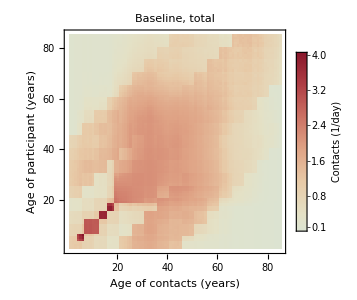
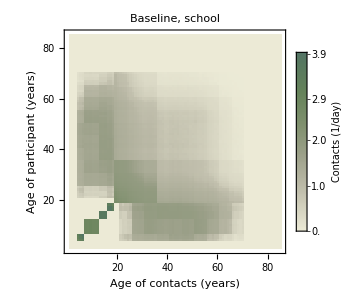
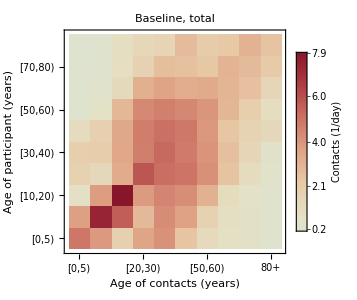
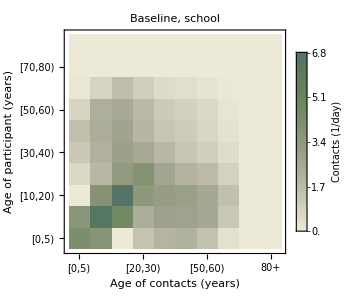
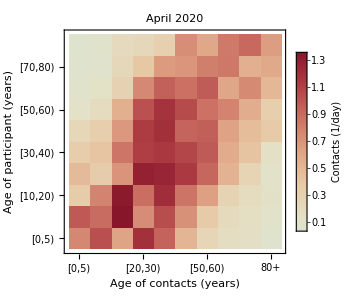
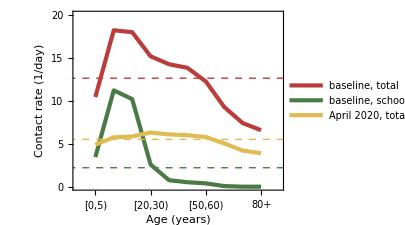
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(* Demographic data for 86+
https://www.pordata.pt/Portugal/Popula%C3%A7%C3%A3o+residente++m%C3%A9dia+anual+total+e+por+grupo+et%C3%A1rio-10 *)
demog86Plus = 316442;

(* Getting the ratio of lockdown contacts based on NL data *)
contactDataNLBefore10=Import["../data/NL_CONTACT_MATRIX_BEFORE_10.csv"];
contactDataNLAfter10=Import["../data/NL_CONTACT_MATRIX_AFTER_10.csv"];
contactRatioNL10=contactDataNLAfter10/contactDataNLBefore10;
demographyData10=Flatten[Import["../data/PT_DEMOGRAPHY_DATA_10.xlsx"]];

(* Function transforming the 1x86 age groups to 1x10 *)
transformList86to10[list85_]:=Total/@Join[Partition[list85,5]⟦1;;2⟧,Partition[list85,10]⟦2;;⟧,{list85⟦81;;⟧}];
demographyData86=Append[demographyData85, demog86Plus];
demographyData10Derived=transformList86to10[demographyData86];


(* Creating the 86x86 contact matrices *)
transformMatrix85to86[mat85_]:=Join[Join[mat85,{mat85⟦85⟧}],List/@(Join[mat85,{mat85⟦85⟧}]⟦All,85⟧ demographyData86⟦86⟧/demographyData86⟦85⟧), 2];

contactDataBefore86=transformMatrix85to86[contactDataBefore85];
schoolContactDataBefore86=transformMatrix85to86[schoolContactDataBefore85];


(* Creating the 10x10 contact matrices*)
transformMatrix86to10[mat86_] :=transformList86to10[Transpose[transformList86to10[Transpose[mat86]]] demographyData86]/demographyData10Derived;
contactDataBefore10=transformMatrix86to10[contactDataBefore86];
contactDataAfter10=contactDataBefore10 * contactRatioNL10 ;
schoolContactDataBefore10=transformMatrix86to10[schoolContactDataBefore86];


(* Assigning parameter variables *)
contactRates:=
Flatten[Table[{Subscript[b,{k,l}]->contactDataBefore10⟦k,l⟧,Subscript[a,{k,l}]->contactDataAfter10⟦k,l⟧,
Subscript[s, {k, l}]->schoolContactDataBefore10[[k,l]]},{k,1,numAgeGroups},{l,1,numAgeGroups}]];


(* Get the total contacts per participant *)
calculateContactsAgeGroupsBefore=calculateTotalContsPerPar[contactDataBefore10, numAgeGroups];
calculateSchoolContactsAgeGroupsBefore=calculateTotalContsPerPar[schoolContactDataBefore10, numAgeGroups];
calculateContactsAgeGroupsAfter=calculateTotalContsPerPar[contactDataAfter10, numAgeGroups];

(* Get the average contacts per participant *)
calculateAverageContactRateBefore=Sum[calculateContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
calculateAverageContactRateSchoolsBefore=Sum[calculateSchoolContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
calculateAverageContactRateAfter=Sum[calculateContactsAgeGroupsAfter⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];


(* Plotting *)
figTotalConmat = plotMatrix[contactDataBefore85, "ThermometerColors" ,"Baseline, total", "contact", ImagePadding->{{70, 0}, {Automatic,0}}];
figSchoolConmat = plotMatrix[schoolContactDataBefore85, ColorData[{"AlpineColors", {1.15,0.45}}] ,"Baseline, school","contact", ImagePadding->{{70, 0}, {Automatic,0}}];
figContactMatrixBefore = plotMatrix[contactDataBefore10, "ThermometerColors" ,"Baseline, total", "contact"];
figSchoolContactMatrixBefore = plotMatrix[schoolContactDataBefore10, ColorData[{"AlpineColors", {1.15,0.45}}] ,"Baseline, school","contact"];
figContactMatrixAfter = plotMatrix[contactDataAfter10, "ThermometerColors", "April 2020", "contact"];
figTotalContPerAge =
plotThickLine[{calculateContactsAgeGroupsBefore, 
calculateSchoolContactsAgeGroupsBefore,
calculateContactsAgeGroupsAfter},{colorDarkRed, colorDarkGreen, colorYellow},"","Age (years)","Contact rate (1/day)",{"baseline, total", "baseline, schools", "April 2020, total"},
"contacts",
{calculateAverageContactRateBefore, calculateAverageContactRateSchoolsBefore, calculateAverageContactRateAfter}, 
{{0, 11}, {0, 20}}, 
ImagePadding->{{40, Automatic}, {Automatic, Automatic}}] ;

figContsA = plotWithLetter[figTotalConmat, "A"];
figContsB = plotWithLetter[figSchoolConmat, "B"];
figContsC = plotWithLetter[figContactMatrixBefore, "C"];
figContsD = plotWithLetter[figSchoolContactMatrixBefore, "D"];
figContsE = plotWithLetter[figContactMatrixAfter, "E"];
figContsF = plotWithLetter[figTotalContPerAge, "F"];
figConts = Grid[{{figContsA, figContsB}, {figContsC, figContsD}, {figContsE, figContsF}}];
If[ifShowFigs, figConts]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CONTACTS",  exportFormat[[i]]],figConts], {i, 1, Length[exportFormat]}]];
```

## Hospitalization data and estimated parameters

### ESTIMATED PARAMETERS

```mathematica
(* Importing estimated parameters *)
estimatesData=Import["../data/PARAMETER_ESTIMATES.csv"];
headerParameters=estimatesData⟦1⟧;
estimatesData=Drop[estimatesData,1];


(* Assigning parameters *)
probabOfTransmEpsilon[sample_]:=ϵ->estimatesData⟦sample,1⟧;
probabOfTransmZeta[sample_]:=ζ-> estimatesData⟦sample,2⟧;
hospitalizationRate[sample_]:=Table[Subscript[ν,k]->estimatesData⟦sample,2+k⟧,{k,1,numAgeGroups}];
susceptibility[sample_]:=Flatten[Join[
Table[Subscript[β,k]->estimatesData⟦sample,14⟧ ,{k,1,3}],
Table[Subscript[β,k]->estimatesData⟦sample,15⟧ ,{k,4,7}],
Table[Subscript[β,k]->estimatesData⟦sample,16⟧ ,{k,8,10}]]];
latencyRate[sample_]:=α->estimatesData⟦sample,18⟧;
recoveryRate[sample_]:=γ->estimatesData⟦sample,19⟧;
rOverDisp[sample_]:=estimatesData⟦sample,17⟧;
logFuncParams[sample_]:={Subscript[xx, 0]-> estimatesData⟦sample,20⟧,Subscript[K, 0]-> estimatesData⟦sample,21⟧,Subscript[xx, 1]-> estimatesData⟦sample,22⟧,Subscript[K, 1]-> estimatesData⟦sample,23⟧,Subscript[xx, 2]-> estimatesData⟦sample,24⟧,Subscript[K, 2]-> estimatesData⟦sample,25⟧,Subscript[xx, 3]-> estimatesData⟦sample,26⟧,Subscript[K, 3]-> estimatesData⟦sample,27⟧,Subscript[xx, 4]-> estimatesData⟦sample,28⟧,Subscript[K, 4]-> estimatesData⟦sample,29⟧};
uParams[sample_]:={Subscript[u, 1]-> estimatesData⟦sample,30⟧,Subscript[u, 2]-> estimatesData⟦sample,31⟧,Subscript[u, 3]-> estimatesData⟦sample,32⟧,Subscript[u, 4]-> estimatesData⟦sample,33⟧} ;
totalPop:=Table[Subscript[NN,k]-> demographyData10⟦k⟧,{k,listAgeGroups}];
initConds[sample_]:=Flatten[Table[{Subscript[S0,k]-> 1-estimatesData⟦sample,13⟧,Subscript[EE0,k]-> 0.5 estimatesData⟦sample,13⟧,Subscript[II0,k]-> 0.5 estimatesData⟦sample,13⟧,Subscript[R0,k]-> 0,Subscript[H0,k]-> 0},{k,listAgeGroups}]];


(* Table for all parameters *)
parameters[sample_]:=
Flatten[{contactRates,totalPop,probabOfTransmEpsilon[sample],probabOfTransmZeta[sample],hospitalizationRate[sample],initConds[sample],susceptibility[sample],logFuncParams[sample],uParams[sample],latencyRate[sample],recoveryRate[sample]}];


(* Table of parameters with just the values *)parameterConstVals = {estimatesData⟦All,1⟧ 100,estimatesData⟦All,2⟧,estimatesData⟦All,13⟧ Total[demographyData10],estimatesData⟦All,14⟧,estimatesData⟦All,15⟧,estimatesData⟦All,17⟧,1/estimatesData⟦All,18⟧,1/estimatesData⟦All,19⟧};
parameterTVals = {estimatesData⟦All,20⟧,estimatesData⟦All,22⟧,estimatesData⟦All,24⟧,estimatesData⟦All,26⟧,estimatesData⟦All,28⟧};
parameterKVals = {estimatesData⟦All,21⟧,estimatesData⟦All,23⟧,estimatesData⟦All,25⟧,estimatesData⟦All,27⟧,estimatesData⟦All,29⟧};
parameterUVals = {estimatesData⟦All,30⟧,estimatesData⟦All,31⟧,estimatesData⟦All,32⟧,estimatesData⟦All,33⟧};
parameterHospRateVals = Table[365 estimatesData⟦All,2+i⟧,{i,1,numAgeGroups}];
```

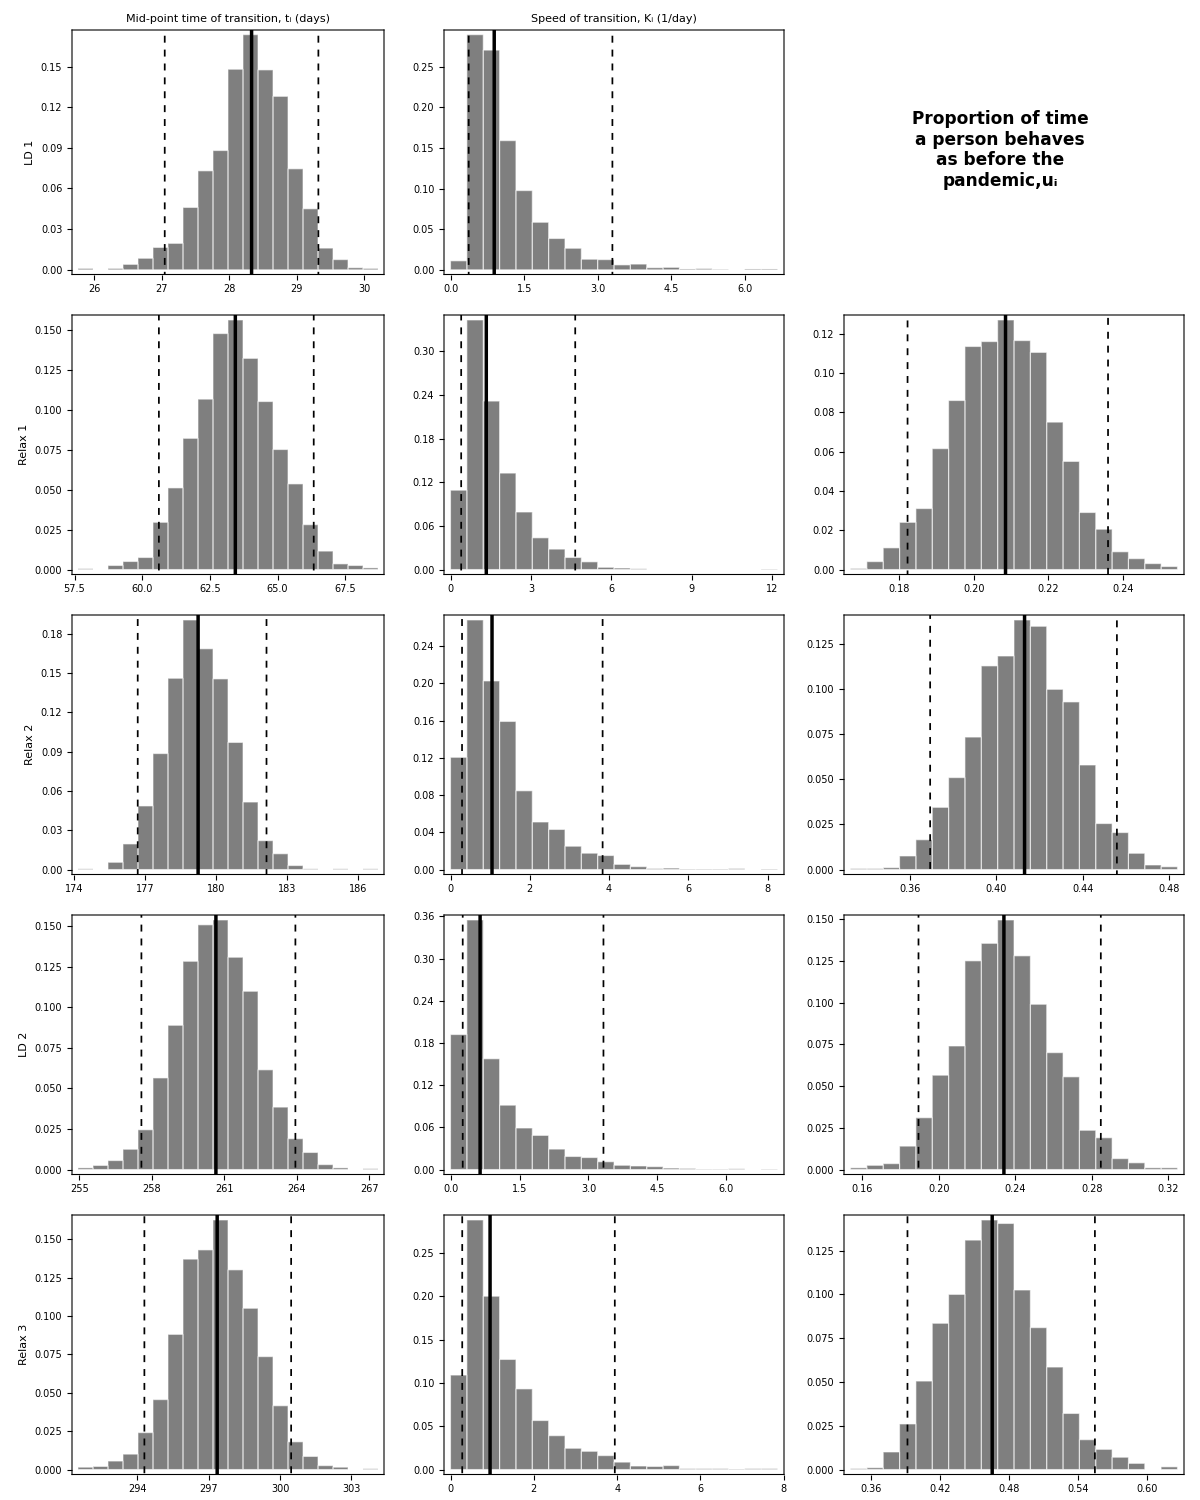

```mathematica
figT = Table[plotWithLetter[plotHistogram[parameterTVals[[i]], If[i == 1, Style["Mid-point time of transition, \nt_i (days)", Bold], ""],
"", Style[diagramLabelsShort[[i]], Bold], Black, False], parameterTXLabel[[i]], "right", sizeFontBig],{i, 1, Length[parameterTVals]}];
figK = Table[plotWithLetter[plotHistogram[parameterKVals[[i]], If[i == 1, Style["Speed of transition, \nK_i (1/day)", Bold], ""],"",  "", Black, False], parameterKXLabel[[i]], "right", sizeFontBig],{i, 1, Length[parameterKVals]}];
figU = Table[plotWithLetter[plotHistogram[parameterUVals[[i]], "", "",  "", Black, False], parameterUXLabel[[i]], "right", sizeFontBig],{i, 1, Length[parameterUVals]}];
figU = Prepend[figU, Graphics[Text[Style["Proportion of time\na person behaves\nas before the\npandemic,u_i\n\n\n\n\n", 17, Bold]]]];
figContParams = Grid[Transpose[{figT, figK, figU}]];

If[ifShowFigs, figContParams]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CONTACTS_PARAMETERS",  exportFormat[[i]]],figContParams], {i, 1, Length[exportFormat]}]];
```

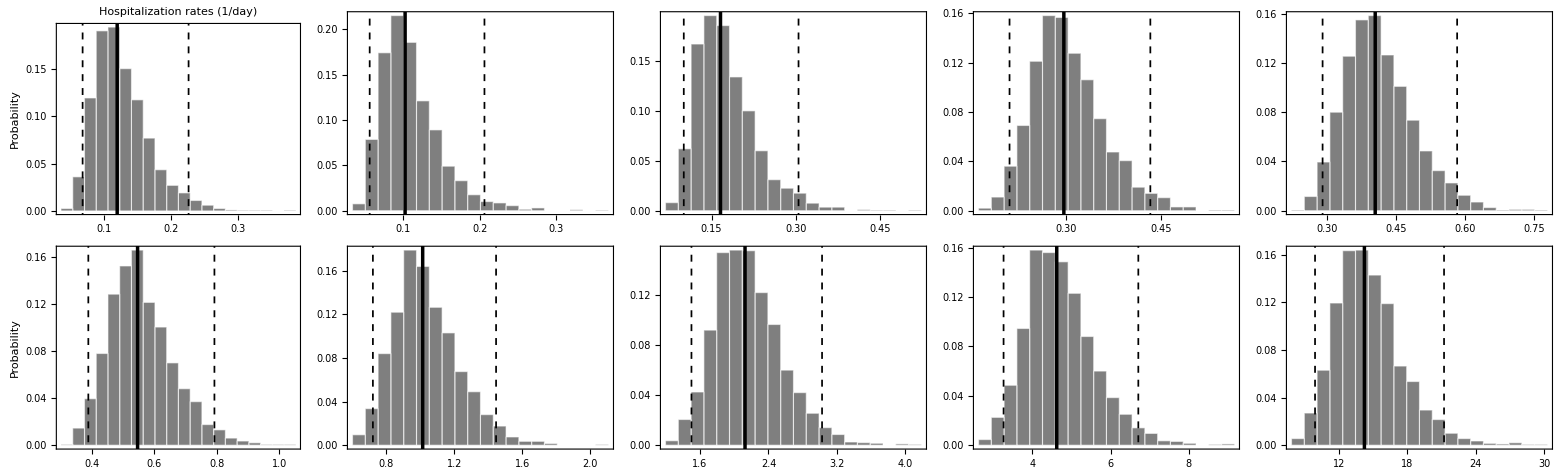

```mathematica
figHospRates = Table[plotWithLetter[plotHistogram[parameterHospRateVals[[i]], If[i == 1, Style["Hospitalization rates (1/day)", Bold], ""],"",  If[i == 1 || i == 6, Style["Probability"],""], Black, False], ageLabelShort[[i]], Scaled[{0.8, 0.9}], sizeFontBig, colorDarkRainbow4AgeGroups[[i]]],{i, 1, Length[parameterHospRateVals]}];
figHospRates = Grid[ArrayReshape[figHospRates, {2,5}]];

If[ifShowFigs, figHospRates]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/HOSP_RATES_PARAMETERS",  exportFormat[[i]]],figHospRates], {i, 1, Length[exportFormat]}]];
```

### HOSPITALIZATION DATA

```mathematica
(* Importing data *)hospitalizationData=Import["../data/PT_HOSPITALIZATION_DATA.csv"];
hospitalizationData=Drop[hospitalizationData,1];
hospitalizationDataTotal =Total[hospitalizationData, {2}];
hospitalizationDataGrouped = {Total[hospitalizationData[[All, 4;;10]], {2}], Total[hospitalizationData[[All, 1;;3]], {2}]};

tickValues=DateRange[{2020,3,1},{2021,1,1},{1,"Month"}][[All,{1,2}]];
ticksss={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;
tickMonths = {#,DateString[DateObject[#],{"MonthNameShort"," ",""}]}&/@tickValues;

(* Transition dates and their respective quantiles *)transitionDates=Table[DayPlus[{2020,02,25}, IntegerPart[Median[estimatesData⟦All,index⟧]]],{index,Range[20,28,2]}]; 
transitionDatesQuantiles025=Table[DayPlus[{2020,02,25}, IntegerPart[Quantile[estimatesData⟦All,index⟧,0.025]]],{index,Range[20,28,2]}]; 
transitionDatesQuantiles975=Table[DayPlus[{2020,02,25}, IntegerPart[Quantile[estimatesData⟦All,index⟧,0.975]]],{index,Range[20,28,2]}]; 
(* Range[20,28,2] are the indices for transition dates *)
transitionDatesLabelsLong={"First lockdown","Relaxation after first lockdown","Further relaxation","Second lockdown","Relaxation due to winter holidays"};
transitionDatesLabelsShort={"LD 1","Relax 1","Relax 2","LD 2","Relax 3"};
```

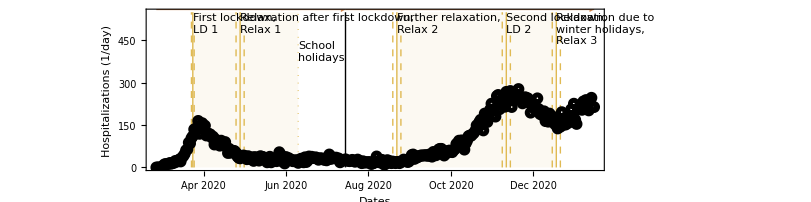

```mathematica
figDiag = plotDiagram[hospitalizationData, ticksss];
If[ifShowFigs, figDiag]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/DIAGRAM",  exportFormat[[i]]],figDiag], {i, 1, Length[exportFormat]}]];
```

## Scenarios

### SCHOOL REDUCTION FACTOR

```mathematica
(* Calculation of the zeta_school parameter for Scenario 2 *)
schoolReductionEquation := 
Table[If[!(k==9 || k==10 ||l==9||l==10||(l==3 && k==1)||(l==1 && k==3)),Solve[(Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}])-reductionFactor Subscript[s,{k,l}]==(Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]),reductionFactor]⟦1⟧⟦1,2⟧],{k,1,numAgeGroups},{l,1,numAgeGroups}];
schoolReductionFactor[sample_]:=zetaSchools->Min[schoolReductionEquation /.Flatten[{contactRates,probabOfTransmZeta[sample],uParams[sample]}]][[1]];

(* Table for all parameters *)
parametersComplete[sample_]:=
Join[parameters[sample],{schoolReductionFactor[sample]}];

(* Saving the zeta_school parameters and obtaining the values *)
SRFFilePath = FileNameJoin[{"../results/solutions/"},StringJoin["SCHOOL_REDUCTION_FACTOR.wxf"]];
schRedFacObtained= Module[{SRF},If[FileExistsQ[SRFFilePath],
SRF = Import[SRFFilePath,"WXF"],
SRF = Table[Min[schoolReductionEquation /.Flatten[{contactRates,probabOfTransmZeta[sample],uParams[sample]}]][[1]], {sample, 1, numAllSamples}];
Export[SRFFilePath,SRF,"WXF","CompressionLevel"->5];
SRF]];
```

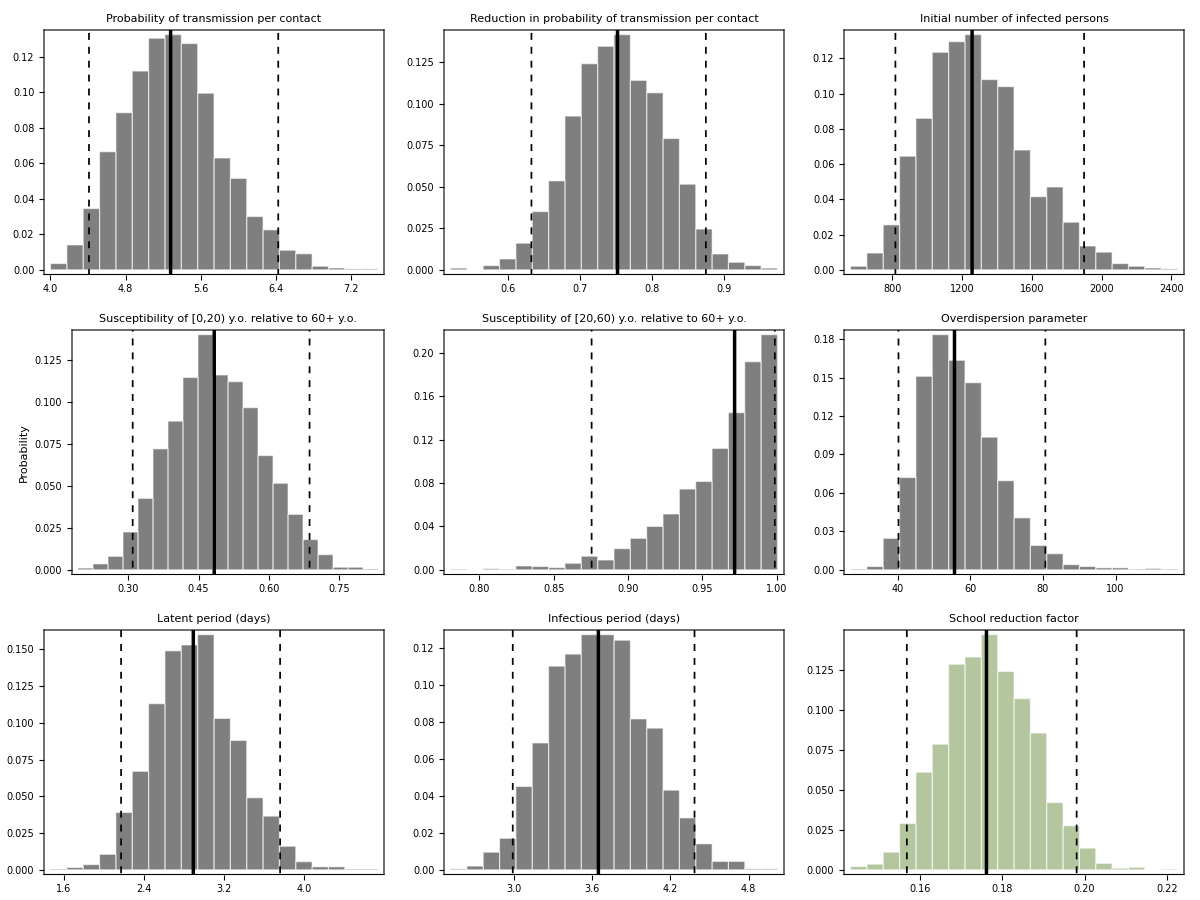

```mathematica
figConstsTables = Table[plotWithLetter[plotHistogram[parameterConstVals[[i]], Style[parameterConstXLabel[[i]], Bold],
"", If[i == 4, Style["Probability", sizeFontBig], ""], Black, False], parameterConstXLabelShort[[i]], Which[i ==3, Scaled[{0.8, 0.9}], i == 5, Scaled[{0.2, 0.9}],True, "right"], sizeFontBig],{i, 1, Length[parameterConstVals]}];
figSRF = plotWithLetter[plotHistogram[schRedFacObtained, Style["School reduction factor", Bold],
"", "", colorGreen, False],"ζ_s", "right", sizeFontBig];
figConstsParams = Grid[ArrayReshape[{figConstsTables, figSRF}, {3,3}]];

If[ifShowFigs, figConstsParams]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CONSTANTS_PARAMETERS",  exportFormat[[i]]],figConstsParams], {i, 1, Length[exportFormat]}]];
```

### EXPRESSIONS FOR CONTACT MATRICES

```mathematica
contactMatrixBaseline[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]);


(* SCENARIO 1 *)
(* Not closing schools during the first lockdown and closing them for school holidays on tstartschoolvacation (10 June)*)
(* ζ or Zeta schools can be introduced to reduce school contacts somewhat for the scenario with not closing schools after the first lockdown in 2020; the logic behind this is that there may be other measures implemented in schools such as masks, physical distancing, etc. *)
contactMatrixScenario1[t_]:=
(Subscript[b,{k,l}]-(*ζ*)Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+ (*ζ*) Subscript[s,{k,l}] (1-1/(1+Exp[-10 (t-timeSchoolVacation)]))+1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))(*(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))*)+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]);

contactMatrixScenario1ZetaSchool[t_]:=
(Subscript[b,{k,l}]-(*ζ*)Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+ ζ 0.5*Subscript[s,{k,l}] (1-1/(1+Exp[-10 (t-timeSchoolVacation)]))+1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))(*(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))*)+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]);

contactMatrixScenario1RelaxedNS[t_]:=
(Subscript[b,{k,l}]-(*ζ*)Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+ (*ζ*) Subscript[s,{k,l}] (1-1/(1+Exp[-10 (t-timeSchoolVacation)]))+1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]);


(* Scenario 2 *)
(* Not opening schools after the summer holidays in 2020 *)
(* Zeta schools must be used to make sure that contacts are non-negative for the scenario with not opening schools after the summer holidays in 2020 *)
contactMatrixScenario2[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]); 

contactMatrixScenario2ZetaZetaS[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-ζ zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-ζ zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-ζ zetaSchools Subscript[s,{k,l}]); 

contactMatrixScenario2RelativeSchool[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) ((Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}])-(Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}])* Subscript[s,{k,l}]/schoolContactsMultiplier) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) ((Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}])- (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}])*Subscript[s,{k,l}]/schoolContactsMultiplier)  (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) ((Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}])-(Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}])*Subscript[s,{k,l}]/schoolContactsMultiplier) ;
```

## Equations and variables

### MODEL EQUATIONS

```mathematica
(* Table of equations *)Table[{eq[Intervention_][1,k]:=Subscript[S,k]'[t]== - Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t],eq[Intervention_][2,k]:=Subscript[EE,k]'[t]== Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-α Subscript[EE,k][t],
eq[Intervention_][3,k]:=Subscript[II,k]'[t]== α Subscript[EE,k][t]-(γ +Subscript[ν,k]) Subscript[II,k][t],
eq[Intervention_][4,k]:=Subscript[R,k]'[t]==γ Subscript[II,k][t],
eq[Intervention_][5,k]:=Subscript[H,k]'[t]==Subscript[ν,k] Subscript[II,k][t]},{k,listAgeGroups}];
NNtot=Sum[Subscript[NN,k],{k,listAgeGroups}];

(* A very ugly if-condition for the contact matrix to use *)contactMatrixWhich[intervention_,t_]:=Which[intervention=="Baseline",contactMatrixBaseline[t],intervention=="Scenario1",contactMatrixScenario1[t],intervention=="Scenario2",contactMatrixScenario2[t],
intervention=="Scenario1_ZetaSchool",contactMatrixScenario1ZetaSchool[t],
intervention=="Scenario1_RelaxedNS",contactMatrixScenario1RelaxedNS[t],
intervention=="Scenario2_ZetaZetaS",contactMatrixScenario2ZetaZetaS[t],
intervention=="Scenario2_RelativeSchool",contactMatrixScenario2RelativeSchool[t],
True,$Failed ];

(* Force of infection *)Table[Subscript[λ,k][intervention][t]=ε Sum[contactMatrixWhich[intervention,t] Subscript[II,l][t]/Subscript[NN,l],{l,listAgeGroups}],{k,listAgeGroups},{intervention,scenarios} (*Iterate over interventions*)];

(* Final table of equations considering the interventions as the argument *)eqs[Intervention_]:=Table[eq[Intervention][j,k],{j,numVariables},{k,listAgeGroups}];
eqsList[Intervention_]:=Flatten[Flatten[eqs[Intervention]]];
```

### VARIABLES

```mathematica
varsS=Table[Subscript[S,k][t],{k,listAgeGroups}];
varsEE=Table[Subscript[EE,k][t],{k,listAgeGroups}];
varsII=Table[Subscript[II,k][t],{k,listAgeGroups}];
varsR=Table[Subscript[R,k][t],{k,listAgeGroups}];
varsH=Table[Subscript[H,k][t],{k,listAgeGroups}];

totS=Total[Total[varsS]];
totEE=Total[Total[varsEE]];
totII=Total[Total[varsII]];
totR=Total[Total[varsR]];
totH=Total[Total[varsH]];

totVars={totS,totEE,totII,totR,totH};
totVarsYLabel={"S(t)","E(t)","I(t)","R(t)","H(t)"};

ageVars={Subscript[S,k][t],Subscript[EE,k][t],Subscript[II,k][t],Subscript[R,k][t],Subscript[H,k][t]};
ageVarsYlab={"S_k(t)","E_k(t)","I_k(t)","R_k(t)","H_k(t)"};

vars=Join[varsS,varsEE,varsII,varsR,varsH];
varsList=Flatten[vars];

hospVars=Table[Subscript[ν,k] (Subscript[II,k][t]),{k,listAgeGroups}];
infIncidenceVars=Table[α (Subscript[EE,k][t]),{k,listAgeGroups}];
```

### SOLVING THE MODEL

```mathematica
ICs=Table[ic[j,k],{j,varNumbers},{k,listAgeGroups}];
ICsList=Flatten[Flatten[ICs]];

Table[ic[1,k]=Subscript[S0,k] Subscript[NN,k]==Subscript[S,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[2,k]=Subscript[EE0,k] Subscript[NN,k]==Subscript[EE,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[3,k]=Subscript[II0,k] Subscript[NN,k]==Subscript[II,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[4,k]=Subscript[R0,k] Subscript[NN,k]==Subscript[R,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[5,k]=Subscript[H0,k] Subscript[NN,k]==Subscript[H,k][t]/.{t->tStart},{k,listAgeGroups}];


solution[Intervention_,pars_]:=NDSolve[Join[eqsList[Intervention],ICsList]/.pars,varsList,{t,tStart,tEnd}, Method->"StiffnessSwitching"];
```

### HOSPITALIZATIONS, INCIDENCES, AND SUSCEPTIBLES

```mathematica
parametersCompleteSampled = Table[parametersComplete[i],{i,1,numAllSamples,stepSamples}];


solutionsForLoop[i_]:=Table[solution[scenarios[[i]],parametersCompleteSampled[[j]]],{j,1,Length[listSamples]}];
solutionsScenarios = importExportScenarioResults["SOLUTIONS", solutionsForLoop, "solutions"];

trajectoriesVarForLoop[var_, i_, label_]:= 
Table[Table[Table[Evaluate[
(If[label === "SUSCEPTIBLE",
(If[k==1,(demographyData10⟦1⟧-86579)/demographyData10⟦1⟧,1] var⟦k⟧)+ If[k==1,86579,0],
var⟦k⟧]/.parametersCompleteSampled⟦j⟧)/.First@solutionsScenarios[[i]]⟦j⟧],
{t,tStart,tEnd,Subscript[t, step]}],
{j,1,Length[listSamples]}],
{k,listAgeGroups}]; 
importExport4Trajectories[var_, label_] := Module[{func},
func[i_] := trajectoriesVarForLoop[var, i,label];
importExportScenarioResults[label, func, "solutions"]];


hospitalizationScenarios=importExport4Trajectories[hospVars, "HOSPITALIZATION"];
incidencesScenarios=importExport4Trajectories[infIncidenceVars, "INCIDENCE"];
susceptibleScenarios =importExport4Trajectories[varsS, "SUSCEPTIBLE"];


NBDReparameterized[m_,f_]:=NegativeBinomialDistribution[f,f/(f+m)];
hospSimulated[var_]:=Table[If[var⟦k⟧⟦sample⟧⟦t⟧>0,RandomVariate[NBDReparameterized[var⟦k⟧⟦sample⟧⟦t⟧,rOverDisp[listSamples⟦sample⟧]]],0],{k,listAgeGroups},{sample,1,Length[listSamples]},{t,1,Dimensions[var]⟦3⟧}];
hospitalizationSimulatedLoop[label_] := Module[{func},
func[i_] := hospSimulated[hospitalizationScenarios[[i]]];
     importExportScenarioResults[label, func, "solutions"]];
hospitalizationSimulatedScenarios = hospitalizationSimulatedLoop["HOSPITALIZATION_SIMULATED"];


summingGroups4Scenarios[variable_, index_] := Transpose[Table[Map[Total[#[[index[[i]], All, All]], {1}] &, variable], {i, 1, Length[index]}]];

hospitalizationScenariosGrouped = summingGroups4Scenarios[hospitalizationScenarios, groupIndex];
hospitalizationScenariosTotal = summingGroups4Scenarios[hospitalizationScenarios, {Range[1, 10]}];
incidencesScenariosGrouped = summingGroups4Scenarios[incidencesScenarios, groupIndex];
incidencesScenariosTotal = summingGroups4Scenarios[incidencesScenarios, {Range[1, 10]}];
susceptibleScenariosGrouped = summingGroups4Scenarios[susceptibleScenarios, groupIndex];
susceptibleScenariosTotal = summingGroups4Scenarios[susceptibleScenarios, {Range[1, 10]}];


hospitalizationSimulatedScenariosGrouped = summingGroups4Scenarios[hospitalizationSimulatedScenarios, groupIndex];
hospitalizationSimulatedScenariosTotal = summingGroups4Scenarios[hospitalizationSimulatedScenarios, {Range[1, 10]}];
```

```mathematica
scatterPlotHospData = DateListPlot[Total[hospitalizationData,{2}], "February 26, 2020", Joined->False, PlotTheme -> "Web",PlotMarkers->{Graphics[{Black,Style[Circle[],Thickness[0.25]]}],5}];
scatterPlotHospDataChild = DateListPlot[Total[hospitalizationData[[All, 1;;3]],{2}], "February 26, 2020", Joined->False, PlotTheme -> "Web",PlotMarkers->{Graphics[{Black,Style[Circle[],Thickness[0.25]]}],5}];
```

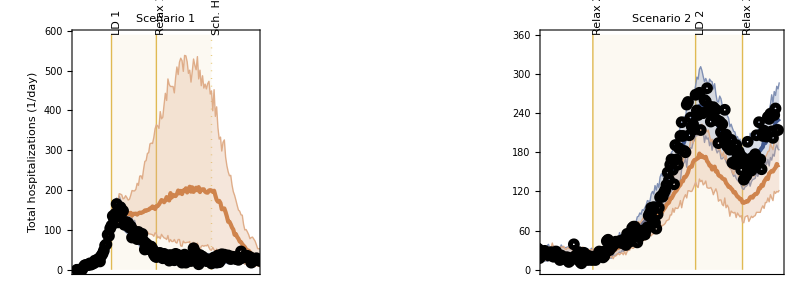
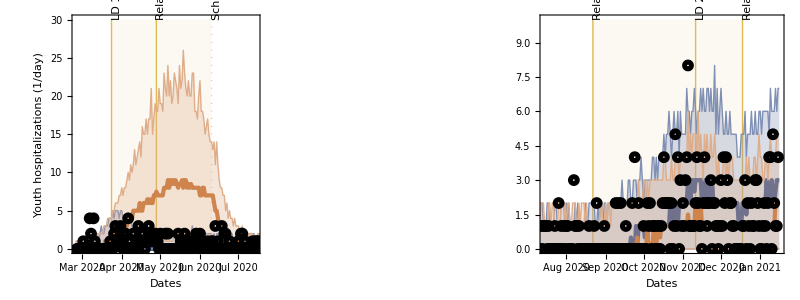

```mathematica
figHospTotal = plotScenarioTrajectories[{hospitalizationSimulatedScenariosTotal[[1,1, All, All]],
hospitalizationSimulatedScenariosTotal[[2,1, All, All]],
hospitalizationSimulatedScenariosTotal[[3,1, All, All]]},"", "Total hospitalizations (1/day)",{"Scenario 1", "Scenario 2"},{None, None},{{0,590},{0,360}},scatterPlotHospData];
figHospChild = plotScenarioTrajectories[{hospitalizationSimulatedScenariosGrouped[[1,1, All, All]],
hospitalizationSimulatedScenariosGrouped[[2,1, All, All]],
hospitalizationSimulatedScenariosGrouped[[3,1, All, All]]},"Dates", "Youth hospitalizations (1/day)",{"", ""},{ticksss,ticksss},{{0,30},{0,10}},scatterPlotHospDataChild, {"C", "D"}];
figHosp = Grid[{{figHospTotal}, {figHospChild}}];
If[ifShowFigs, figHosp]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/HOSPITALIZATIONS_TOTAL_YOUTH",  exportFormat[[i]]],figHosp], {i, 1, Length[exportFormat]}]];
```

```mathematica
seroprevalenceFunc[var_, varindices_, demogindices_] :=
Table[100-100var[[All,varindices[[i]],All,All]]/Total[demographyData10[[demogindices[[i]]]]], {i, 1, Length[varindices]}];

seroprevalenceScenariosTotal = 100-100susceptibleScenariosTotal/Total[demographyData10];

listGrouped = {Range[1,3], Range[4,10]};
seroprevalenceScenariosGrouped = ConstantArray[0, {3,2,100,327}];
Table[seroprevalenceScenariosGrouped[[All, k, All, All]]=
100-100susceptibleScenariosGrouped[[All,k,All,All]]/Total[demographyData10[[listGrouped[[k]]]]];, {k ,1,2}];

seroprevalenceScenarios = ConstantArray[0, {3,10,100,327}];
Table[seroprevalenceScenarios[[All, k, All, All]]=
100-100susceptibleScenarios[[All,k,All,All]]/Total[demographyData10[[k]]];, {k ,1,numAgeGroups}];
```

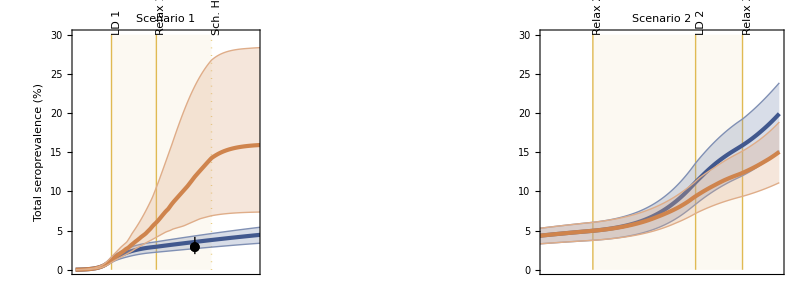
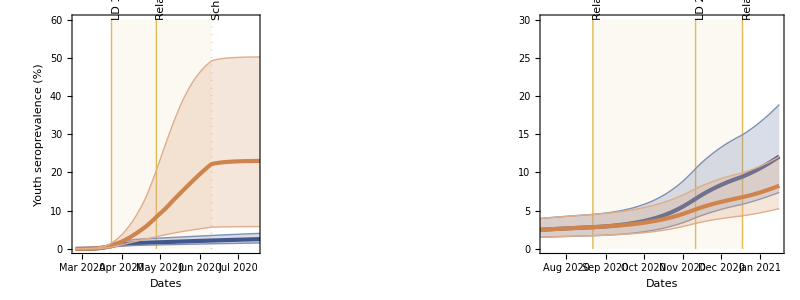

```mathematica
scatterPlotSeroSinglePoint = DateListPlot[{Around[totalMeanSero, {Abs[totalMeanSero - totalLowMeanSero], Abs[totalHighMeanSero-totalMeanSero]}]}, AbsoluteTime["May 28, 2020"], PlotMarkers->{Automatic,10},PlotStyle -> {Black},IntervalMarkers->"Fences",IntervalMarkersStyle->{Black,Thick}, PlotStyle->"Web"];

figSeroTotal= plotScenarioTrajectories[{seroprevalenceScenariosTotal[[1,1, All, All]],
seroprevalenceScenariosTotal[[2,1, All, All]],
seroprevalenceScenariosTotal[[3,1, All, All]]},"","Total seroprevalence (%)",{"Scenario 1","Scenario 2"},{None,None},{{0,30},{0,30}}, scatterPlotSeroSinglePoint];
figSeroChild= plotScenarioTrajectories[{seroprevalenceScenariosGrouped[[1,1, All, All]],
seroprevalenceScenariosGrouped[[2,1, All, All]],
seroprevalenceScenariosGrouped[[3,1, All, All]]},"Dates","Youth seroprevalence (%)",{"",""},{ticksss,ticksss},{{0,60},{0,30}}, Graphics[],{"C", "D"}];
figSero = Grid[{{figSeroTotal}, {figSeroChild}}];
If[ifShowFigs, figSero]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/SEROPREVALENCE_TOTAL_YOUTH",  exportFormat[[i]]],figSero], {i, 1, Length[exportFormat]}]];
```

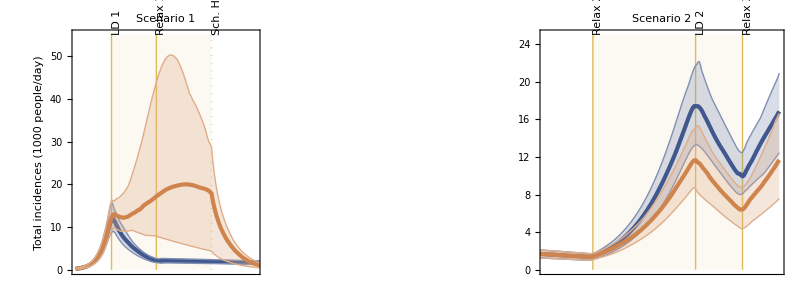
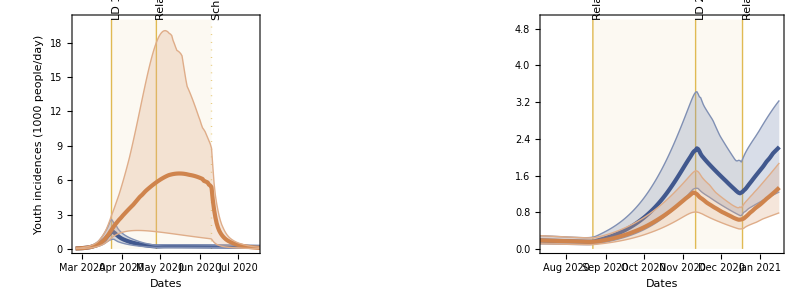

```mathematica
figIncidTotal= plotScenarioTrajectories[{incidencesScenariosTotal[[1,1, All, All]]/1000,
incidencesScenariosTotal[[2,1, All, All]]/1000,
incidencesScenariosTotal[[3,1, All, All]]/1000},"","Total incidences (1000 people/day)",{"Scenario 1","Scenario 2"},{None,None},{{0,55},{0,25}}];
figIncidChild= plotScenarioTrajectories[{incidencesScenariosGrouped[[1,1, All, All]]/1000,
incidencesScenariosGrouped[[2,1, All, All]]/1000,
incidencesScenariosGrouped[[3,1, All, All]]/1000},"Dates","Youth incidences (1000 people/day)",{"",""},{ticksss,ticksss},{{0,20},{0,5}}, Graphics[],{"C", "D"}];
figIncid = Grid[{{figIncidTotal}, {figIncidChild}}];
If[ifShowFigs, figIncid]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/INCIDENCES_TOTAL_YOUTH",  exportFormat[[i]]],figIncid], {i, 1, Length[exportFormat]}]];
```

## Analysis

### AVERAGE CONTACT RATE

```mathematica
trajectoriesContacts[i_, t_, sample_]:=Table[Table[contactMatrixWhich[scenarios[[i]],t]/.parametersCompleteSampled⟦sample⟧/.contactRates, {l, 1, numAgeGroups}], {k, 1, numAgeGroups}];

importExport4Contacts[label_] := Module[{func},
func[i_] := Table[Table[trajectoriesContacts[i, t, j],{t,tStart,tEnd,Subscript[t, step]}],{j,1,Length[listSamples]}];
importExportScenarioResults[label, func, "solutions"]];
contactMatricesScenarios = importExport4Contacts["CONTACTS"];
```

```mathematica
demographyData1010 =Transpose[Table[demographyData10, {i, 1, numAgeGroups}]];
averageContactMatrixTotalScenarios = contactMatricesScenarios;
Do[averageContactMatrixTotalScenarios[[i,j,k,All,All]]=contactMatricesScenarios[[i,j,k,All,All]]*demographyData1010,{i,1,numScenarios},{j,1,numSamples},{k,1,numTimes}];
averageContactsTotalScenarios = Total[averageContactMatrixTotalScenarios, {5}] / Total[demographyData10];
averageContactsTotalScenariosFunc[index_]:=averageContactsTotalScenarios[[index,All,All,All]];

importExportScenarioResults["CONTACTS_AVERAGE", averageContactsTotalScenariosFunc, "solutions"];
```

```mathematica
averageContactsTotal= Total[averageContactsTotalScenarios[[All, All, All, Range[1,10]]], {4}];
averageContactsYouth= Total[averageContactsTotalScenarios[[All, All, All, Range[1,3]]], {4}];
averageContactsAdults =Total[averageContactsTotalScenarios[[All, All, All, Range[4,10]]], {4}];
```

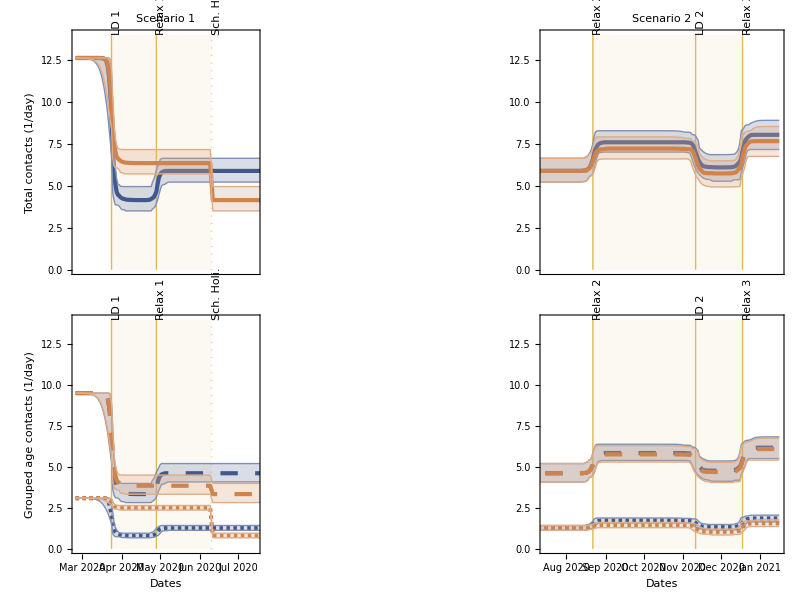

```mathematica
legendGroupedAgesScen1 = {Inset[Graphics[Text[StyleForm["adults, 20+",FontSize->sizeFontSmaller,FontColor->Black]]],{AbsoluteTime["March 8, 2020"], 10},{-0.075, 0}, Alignment->Left],
Inset[Graphics[Text[StyleForm["youth, [0, 20)",FontSize->sizeFontSmaller,FontColor->Black]]],{AbsoluteTime["March 8, 2020"], 3.75},{-0.075, 0}, Alignment->Left]};
legendGroupedAgesScen2 = {Inset[Graphics[Text[StyleForm["adults, 20+",FontSize->sizeFontSmaller,FontColor->Black]]],{AbsoluteTime["August 1, 2020"], 5.75},{-0.075, 0}, Alignment->Left],
Inset[Graphics[Text[StyleForm["youth, [0, 20)",FontSize->sizeFontSmaller,FontColor->Black]]],{AbsoluteTime["August 1, 2020"], 2},{-0.075, 0}, Alignment->Left]};
figAverageContactsTotalScen1 = plotWithLetter[{plotLineWithCrI[averageContactsTotal[[1,All,All]],colorBlue,"Scenario 1","","Total contacts (1/day)",1,None,{0, 14}, 0.5, 500],plotLineWithCrI[averageContactsTotal[[2,All,All]],colorOrange,"","","",1,None,{0, 14}, 0.5, 500]},"A","right"];
figAverageContactsTotalScen2 = plotWithLetter[{plotLineWithCrI[averageContactsTotal[[1,All,All]],colorBlue,"Scenario 2","","",2,None,{0, 14}, 0.5, 500],plotLineWithCrI[averageContactsTotal[[3,All,All]],colorOrange,"","","",2,None,{0, 14}, 0.5, 500]},"B","right"];
figAverageContactsGroupedScen1 = plotWithLetter[{plotLineWithCrI[averageContactsAdults[[1,All,All]],colorBlue,"","Dates","Grouped age contacts (1/day)",1,ticksss,{0, 14}, 0.5, 500, Dashing[{0.025, 0.025}]],plotLineWithCrI[averageContactsAdults[[2,All,All]],colorOrange,"","Dates","",1,ticksss,{0, 14}, 0.5, 500, Dashing[{0.025, 0.025}]],
plotLineWithCrI[averageContactsYouth[[1,All,All]],colorBlue,"","Dates","",1,ticksss,{0, 14}, 0.5, 500, Dashing[{0.005, 0.005}]],plotLineWithCrI[averageContactsYouth[[2,All,All]],colorOrange,
"","Dates","",1,ticksss,{0, 14}, 0.5, 500, Dashing[{0.005, 0.005}]]},"C","right", sizeFontBigger, Black, legendGroupedAgesScen1];
figAverageContactsGroupedScen2 = plotWithLetter[{plotLineWithCrI[averageContactsAdults[[1,All,All]],colorBlue,"","Dates","",2,ticksss,{0, 14}, 0.5, 500, Dashing[{0.025, 0.025}]],plotLineWithCrI[averageContactsAdults[[3,All,All]],colorOrange,"","Dates","",2,ticksss,{0, 14}, 0.5, 500, Dashing[{0.025, 0.025}]],
plotLineWithCrI[averageContactsYouth[[1,All,All]],colorBlue,"","Dates","",2,ticksss,{0, 14}, 0.5, 500, Dashing[{0.005, 0.005}]],plotLineWithCrI[averageContactsYouth[[3,All,All]],colorOrange,
"","Dates","",2,ticksss,{0, 14}, 0.5, 500, Dashing[{0.005, 0.005}]]},"D","right", sizeFontBigger, Black,legendGroupedAgesScen2];
figAverageContacts = Grid[{{figAverageContactsTotalScen1,  figAverageContactsTotalScen2},{figAverageContactsGroupedScen1, figAverageContactsGroupedScen2}}];
If[ifShowFigs, figAverageContacts]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CONTACTS_AVERAGE",  exportFormat[[i]]],figAverageContacts], {i, 1, Length[exportFormat]}]];
```

```mathematica
(* Creating the 2x2 contact matrices*)
transformList10to2[list10_]:=Total/@Join[{list10[[1;;3]]},{list10[[4;;10]]}];
demographyData2 = transformList10to2[demographyData10];
transformMatrix10to2[mat10_] :=transformList10to2[Transpose[transformList10to2[Transpose[mat10]]] demographyData10]/demographyData2;

twoContactMatrixScenarios = ConstantArray[0, {numScenarios, numSamples, numTimes, 2,2}];
Do[twoContactMatrixScenarios[[i,j,k,All,All]]=transformMatrix10to2[contactMatricesScenarios[[i,j,k,All,All]]],{i,1,numScenarios},{j,1,numSamples},{k,1,numTimes}];

middleOfPeriodsScen1Dates = {"March 1, 2020", "April 1, 2020", "June 1, 2020", "July 1, 2020"};
middleOfPeriodsScen2Dates = {"August 1, 2020", "October 1, 2020", "December 1, 2020", "January 1, 2020"};
dateDifference[dateString_String]:=DateDifference[DateObject[{2020, 2,25}],DateObject[dateString],"Day"][[1]];
scen1Differences=dateDifference/@middleOfPeriodsScen1Dates;
scen2Differences=dateDifference/@middleOfPeriodsScen2Dates;

twoConMatMedian = Median[Transpose[twoContactMatrixScenarios]];
twoConMatLower= Quantile[Transpose[twoContactMatrixScenarios], 0.025];
twoConMatUpper = Quantile[Transpose[twoContactMatrixScenarios], 0.975];
```

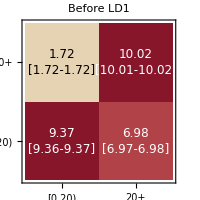
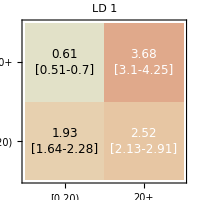
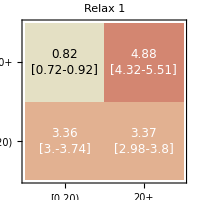
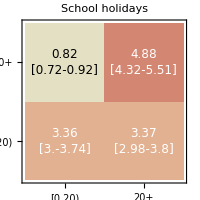
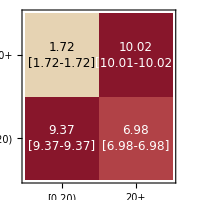
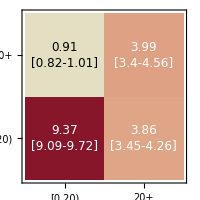
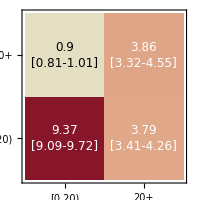
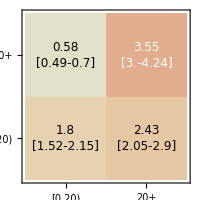
Age of participant (years) | Baseline | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Scenario 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Age of contact (years)

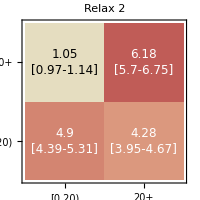
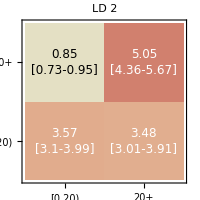
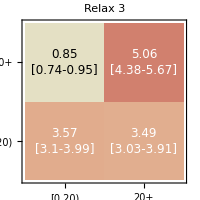
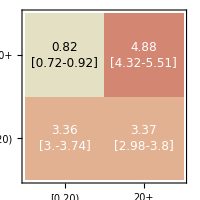
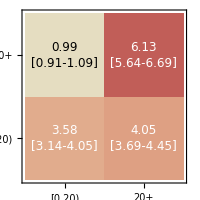
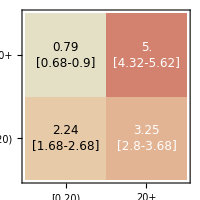
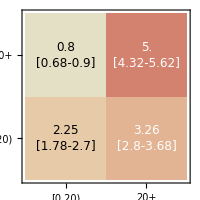
Age of participant (years) | Baseline | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Scenario 2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Age of contact (years)

```mathematica
scen1CMTitles = Flatten[{"Before LD1", diagramLabelsShort[[1;;2]], "School holidays"}];
scen2CMTitles = diagramLabelsShort[[2;;5]];

figTwoCMScen1= Table[Table[plotMatrix2[twoConMatMedian[[j,scen1Differences[[i]]]],
twoConMatLower[[j,scen1Differences[[i]]]],
twoConMatUpper[[j,scen1Differences[[i]]]],
If[j === 1,scen1CMTitles[[i]], ""],False], {i, 1, Length[scen1Differences]}], {j, {1, 2}}];
figTwoCMScen2= Table[Table[plotMatrix2[twoConMatMedian[[j,scen2Differences[[i]]]],
twoConMatLower[[j,scen2Differences[[i]]]],
twoConMatUpper[[j,scen2Differences[[i]]]],
If[j === 1,scen2CMTitles[[i]], ""],False], {i, 1, Length[scen2Differences]}], {j, {1, 3}}];

fig2CMScenario1 = Grid[{{Style[Rotate["Age of participant (years)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],
Grid[{Flatten[{
Style[Rotate["Baseline", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figTwoCMScen1[[1]]}], Flatten[{Style[Rotate["Scenario 1", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figTwoCMScen1[[2]]}]}]}, {"",Style["Age of contact (years)",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, fig2CMScenario1]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CONTACTS_MATRIX_SCEN1",  exportFormat[[i]]],fig2CMScenario1], {i, 1, Length[exportFormat]}]];

fig2CMScenario2 = Grid[{{Style[Rotate["Age of participant (years)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],
Grid[{Flatten[{
Style[Rotate["Baseline", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figTwoCMScen2[[1]]}], Flatten[{Style[Rotate["Scenario 2", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figTwoCMScen2[[2]]}]}]}, {"",Style["Age of contact (years)",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, fig2CMScenario2]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CONTACTS_MATRIX_SCEN2",  exportFormat[[i]]],fig2CMScenario2], {i, 1, Length[exportFormat]}]];
```

### TIME-VARYING REPRODUCTION NUMBER

```mathematica
eqNumbersSusceptible = eqNumbers[[1 ;; numAgeGroups]];
eqNumbersExposed = eqNumbers[[numAgeGroups + 1 ;; 2 numAgeGroups]];
eqNumbersInfectious = eqNumbers[[2 numAgeGroups + 1 ;; 3 numAgeGroups]];

NGM= Table[Table[((-1/D[eqsList[scenarios[[i]]]⟦p,2⟧,varsList⟦p⟧] D[eqsList[scenarios[[i]]]⟦k,2⟧,varsList⟦p⟧])),{k,eqNumbersExposed},{p,eqNumbersInfectious}], {i, 1, Length[scenarios]}];
```

```mathematica
substituteNGM[scenNum_, sample_, time_] :=
((NGM[[scenNum]]/. (First@solutionsScenarios[[scenNum]][[sample]])[[eqNumbersSusceptible]]) /. parametersCompleteSampled[[sample]]) /. t -> time;

NGMForLoop[i_] :=Table[Table[substituteNGM[i, j, t], {t,tStart,tEnd,Subscript[t, step]}],{j,1,Length[listSamples]}];
NGMScenarios = importExportScenarioResults["NGM", NGMForLoop, "analysis"];

eigenAllFirst[matrix_] := Module[{valRight, valLeft}, 
valRight = Eigensystem[matrix, 1];
valLeft = Eigensystem[Transpose[matrix], 1]; 
{valRight[[1]][[1]], 
valRight[[2]][[1]],
valLeft[[2]][[1]]}];
RtForLoop[i_] :=Table[Table[eigenAllFirst[NGMScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
RtScenarios = importExportScenarioResults["EIGEN", RtForLoop, "analysis"];
```

### TIME-VARYING CUMULATIVE ELASTICITIES

```mathematica
sensMatrix[eigen_]:=
Module[{eigenRight, eigenLeft},
eigenRight = eigen[[2]];
eigenLeft = eigen[[3]];Outer[Times,eigenLeft,eigenRight]/Dot[eigenLeft, eigenRight]];

elasMatrix[eigen_, NGM_, sens_] := 
Module[{R},
R = eigen[[1]];
NGM * sens / R];

cumuElasMatrix[elas_] :=
Total[elas,{1}];

sensForLoop[i_] :=Table[Table[sensMatrix[RtScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
elasForLoop[i_] :=Table[Table[elasMatrix[RtScenarios[[i, j, t]], NGMScenarios[[i, j, t]], sensScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
cumuElasForLoop[i_] := Table[Table[cumuElasMatrix[elasScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];

sensScenarios = importExportScenarioResults["SENSITIVITY", sensForLoop, "analysis"];
elasScenarios = importExportScenarioResults["ELASTICITY", elasForLoop, "analysis"];
cumuElasScenarios = importExportScenarioResults["CUMUELAS", cumuElasForLoop, "analysis"];


cumuElasGroupedScenarios = Table[Table[Total[cumuElasScenarios[[scen]][[sample]][[time]][[groupIndex[[i]]]]], {i, 1, Length[groupIndex]}], {scen, 1, Length[scenarios]}, {sample, 1, Length[listSamples]}, {time, 1, numTimes}];
```

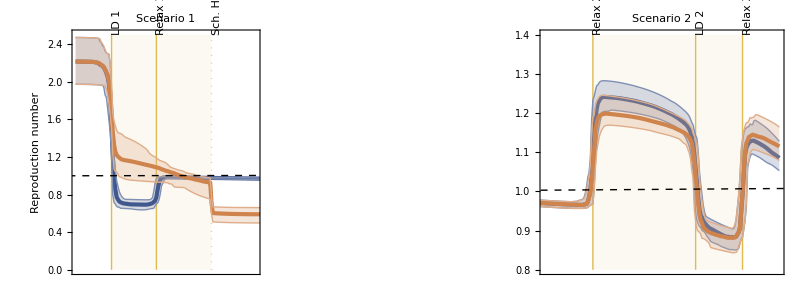
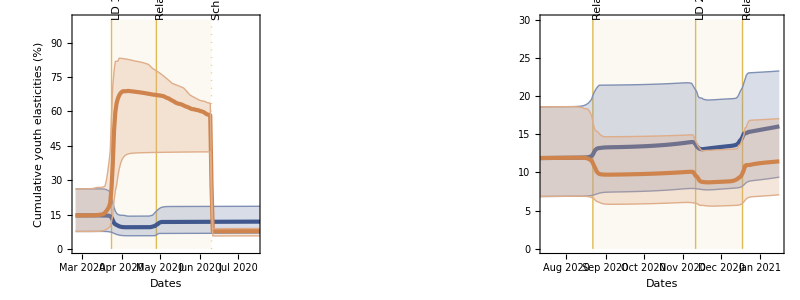

```mathematica
tickValues=DateRange[{2020,3,1},{2021,1,1},{1,"Month"}][[All,{1,2}]];
ticksss={#,Rotate[DateString[#,{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;

Rt1 = Graphics[{Dashed,Black,InfiniteLine[{AbsoluteTime["February 26, 2020"],1},{AbsoluteTime["January 15, 2020"],1}]}];

figRt = plotScenarioTrajectories[{RtScenarios[[1,All,All,1]],
RtScenarios[[2,All,All,1]],
RtScenarios[[3,All,All,1]]},"", "Reproduction number",{"Scenario 1","Scenario 2"},{None, None},{{0,2.5},{0.8,1.4}}, Rt1, {"A", "B"}, "right"];
figCumuElas = plotScenarioTrajectories[{100cumuElasGroupedScenarios[[1,All,All,1]],
100cumuElasGroupedScenarios[[2,All,All,1]],
100cumuElasGroupedScenarios[[3,All,All,1]]},"Dates","Cumulative youth elasticities (%)",{"",""},{ticksss,ticksss},{{0,100},{0, 30}},  Graphics[],{"C", "D"}, "right"];
figRtCumuElasChild = Grid[{{figRt}, {figCumuElas}}];

If[ifShowFigs, figRtCumuElasChild]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/RT_CUMU_ELAS",  exportFormat[[i]]],figRtCumuElasChild], {i, 1, Length[exportFormat]}]];
```

```mathematica
cumuElasGroupedScenariosMean = Mean[Transpose[Re[cumuElasGroupedScenarios]]];
cumuElasScenariosMean = Mean[Transpose[Re[cumuElasScenarios]]];

figCumuElasMean1 = plotStackedLinesWhole[100Transpose[cumuElasScenariosMean[[1]]],100cumuElasGroupedScenariosMean[[2,All,1]], 1, False, "Mean cumulative elasticities (%)", "Scenario 1", "", None];
figCumuElasMean2 = plotStackedLinesWhole[100Transpose[cumuElasScenariosMean[[1]]],100cumuElasGroupedScenariosMean[[3,All,1]], 2, True, "", "Scenario 2", "", None];

figCumuElasMeanAgeGroups = Grid[{{figCumuElasMean1,figCumuElasMean2}}];
If[ifShowFigs, figCumuElasMeanAgeGroups];
```

```mathematica
cumuElasDiffGroupedScenariosMeanScen1 = Transpose[Mean[Re[cumuElasGroupedScenarios[[2]]-cumuElasGroupedScenarios[[1]]]]];
cumuElasDiffGroupedScenariosMeanScen2 = Transpose[Mean[Re[cumuElasGroupedScenarios[[3]]-cumuElasGroupedScenarios[[1]]]]];
cumuElasDiffScenariosMeanScen1 = Transpose[Mean[Re[cumuElasScenarios[[2]]-cumuElasScenarios[[1]]]]];
cumuElasDiffScenariosMeanScen2 = Transpose[Mean[Re[cumuElasScenarios[[3]]-cumuElasScenarios[[1]]]]];

Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]
figCumuElasMean1Diff = plotStackedLinesMoving[100cumuElasDiffScenariosMeanScen1, 1, False, {-70,70}, "Mean cumu. elas. difference (%)"];
figCumuElasMean2Diff = plotStackedLinesMoving[100cumuElasDiffScenariosMeanScen2, 2, True, {-10,10}];
figCumuElasMeanAgeGroupsDiff = Grid[{{figCumuElasMean1Diff,figCumuElasMean2Diff}}];
If[ifShowFigs, figCumuElasMeanAgeGroupsDiff];
```

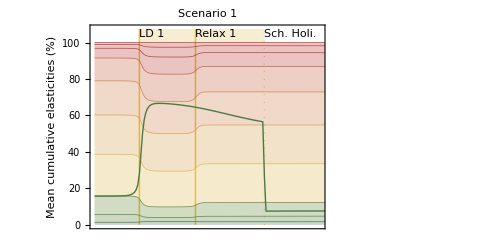
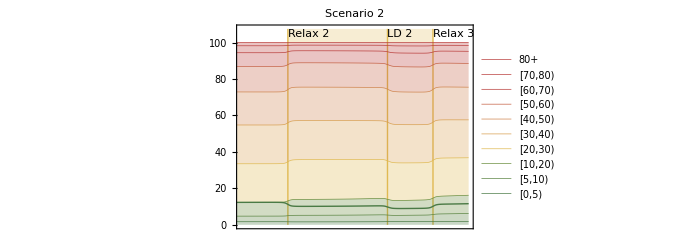
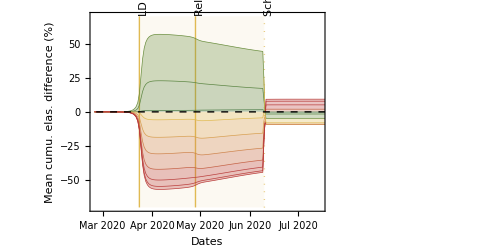
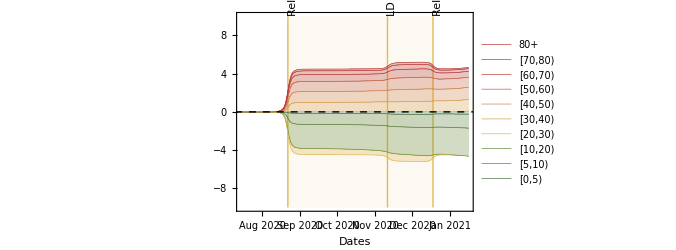
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
figCumuElasMeanAgeGroupsAll = Grid[{{figCumuElasMeanAgeGroups}, {figCumuElasMeanAgeGroupsDiff}}];
If[ifShowFigs, figCumuElasMeanAgeGroupsAll]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CUMU_ELAS_MEAN_AGES",  exportFormat[[i]]],figCumuElasMeanAgeGroupsAll], {i, 1, Length[exportFormat]}]];
```

```mathematica
PlotElast[trajelas_,tstartplot_,tendplot_,plotlabel_,panellab_,ylabel_,ticks_]:=Show[StackedDateListPlot[Transpose[trajelas],{"February 25, 2020",Automatic,{0,0,Subscript[t, step]}},FrameTicks->{{Automatic,None},{ticks,None}},AspectRatio->AspRat,ImageSize->0.8 ImSize,PlotRangePadding->None,
Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,17],PlotRange->{{tstartplot,tendplot},{0,1}},
AxesOrigin->{"February 25, 2020",0},FrameLabel-> {{ylabel,None},{None,None}},PlotStyle->(*ChartStyleColors*)ColorData["DarkRainbow"]/@Rescale[AgeGroups⟦1;;10⟧],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},Prolog->{Join[{Directive[{Darker[Green]}]},Table[InfiniteLine[{TransitionDates⟦i⟧,0},{0,1}],{i,1,Length[TransitionDates]}]](*,{Directive[{Thick,Red}],InfiniteLine[{{0,1},{2,1}}]}*)(*,Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]]*)},ImagePadding->{{47.5, 2.5}, {Automatic, Automatic}},Joined->True,PlotLabel->Style[Row[{plotlabel}],Black,17],PlotLegends->If[(*panellab=="d"||*)panellab=="d",(*Placed[*)BarChartLegends⟦1;;⟧(*,*)(*{After,Top}*)(*{Scaled[ {{1.1, 0.5}, {0.5,0.5 }}]}]*),None]],Graphics[Text[StyleForm[panellab,FontSize->26],Scaled[{0.9,0.9}]]]]
```

## Extra figures for two scenarios

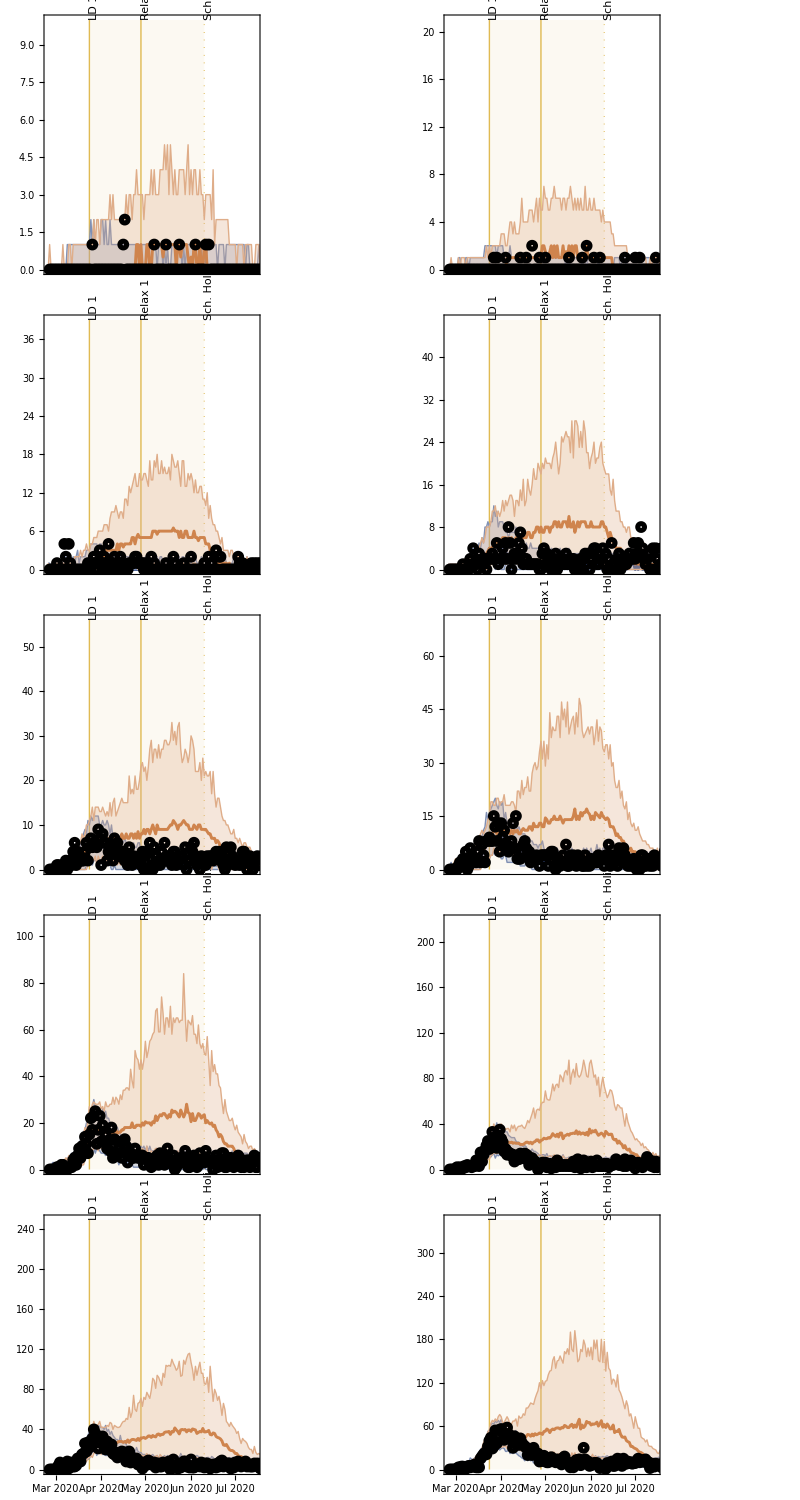
Hospitalizations (1/day) | -Graphics-
 | Dates

```mathematica
scatterPlotHospData10Groups[k_] := DateListPlot[hospitalizationData[[All,k]], "February 26, 2020", Joined->False, PlotTheme -> "Web",PlotMarkers->{Graphics[{Black,Style[Circle[],Thickness[0.25]]}],5}];

figHosp10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[hospitalizationSimulatedScenarios[[2, k, All, All]]];
maxRange = maxVal+10^Floor[Log10[Abs[maxVal]]];
plotWithLetter[{plotLineWithCrI[hospitalizationSimulatedScenarios[[1, k, All, All]],colorBlue,"","","",1,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[hospitalizationSimulatedScenarios[[2, k, All, All]],colorOrange],
scatterPlotHospData10Groups[k]},ageLabelShort[[k]],"right", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figHosp10Scen1 = Grid[{{Style[Rotate["Hospitalizations (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figHosp10Scen1, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figHosp10Scen1]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/HOSPITALIZATIONS_10_SCEN1",  exportFormat[[i]]],figHosp10Scen1], {i, 1, Length[exportFormat]}]];
```

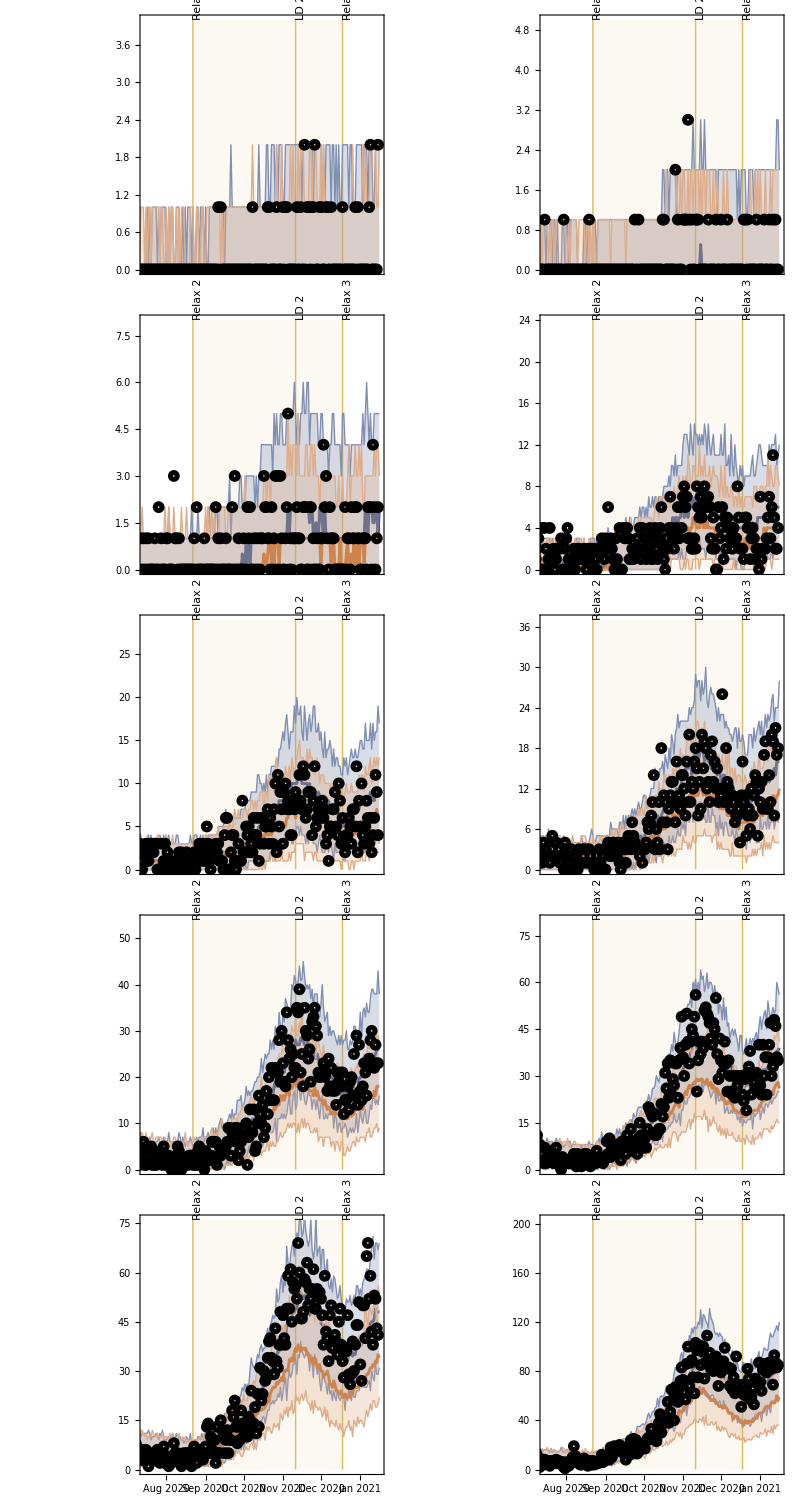
Hospitalizations (1/day) | -Graphics-
 | Dates

```mathematica
figHosp10Scen2=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[hospitalizationSimulatedScenarios[[3, k, All, All]]];
maxRange = maxVal+10^Floor[Log10[Abs[maxVal]]];
plotWithLetter[{plotLineWithCrI[hospitalizationSimulatedScenarios[[1, k, All, All]],colorBlue,"","","",2,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[hospitalizationSimulatedScenarios[[3, k, All, All]],colorOrange],
scatterPlotHospData10Groups[k]},ageLabelShort[[k]],"left", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figHosp10Scen2 = Grid[{{Style[Rotate["Hospitalizations (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figHosp10Scen2, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figHosp10Scen2]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/HOSPITALIZATIONS_10_SCEN2",  exportFormat[[i]]],figHosp10Scen2], {i, 1, Length[exportFormat]}]];
```

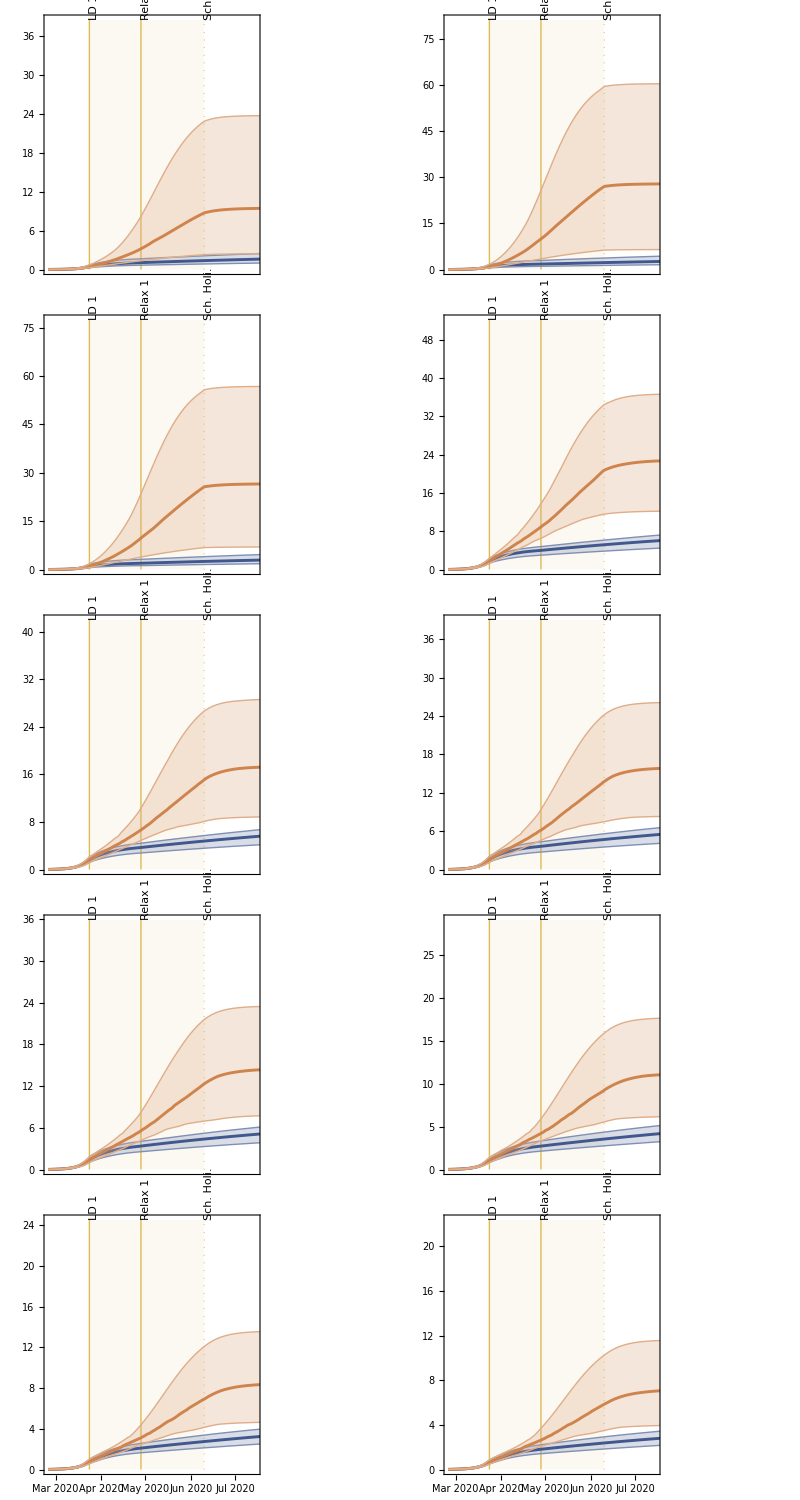
Seroprevalence (%) | -Graphics-
 | Dates

```mathematica
figSero10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[seroprevalenceScenarios[[2, k, All, All]]];
maxRange = maxVal+Max[1,10^Floor[Log10[Abs[maxVal]]]];
plotWithLetter[{plotLineWithCrI[seroprevalenceScenarios[[1, k, All, All]],colorBlue,"","","",1,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[seroprevalenceScenarios[[2, k, All, All]],colorOrange]},ageLabelShort[[k]],"right", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figSero10Scen1 = Grid[{{Style[Rotate["Seroprevalence (%)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figSero10Scen1, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figSero10Scen1]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/SEROPREVALENCE_10_SCEN1",  exportFormat[[i]]],figSero10Scen1], {i, 1, Length[exportFormat]}]];
```

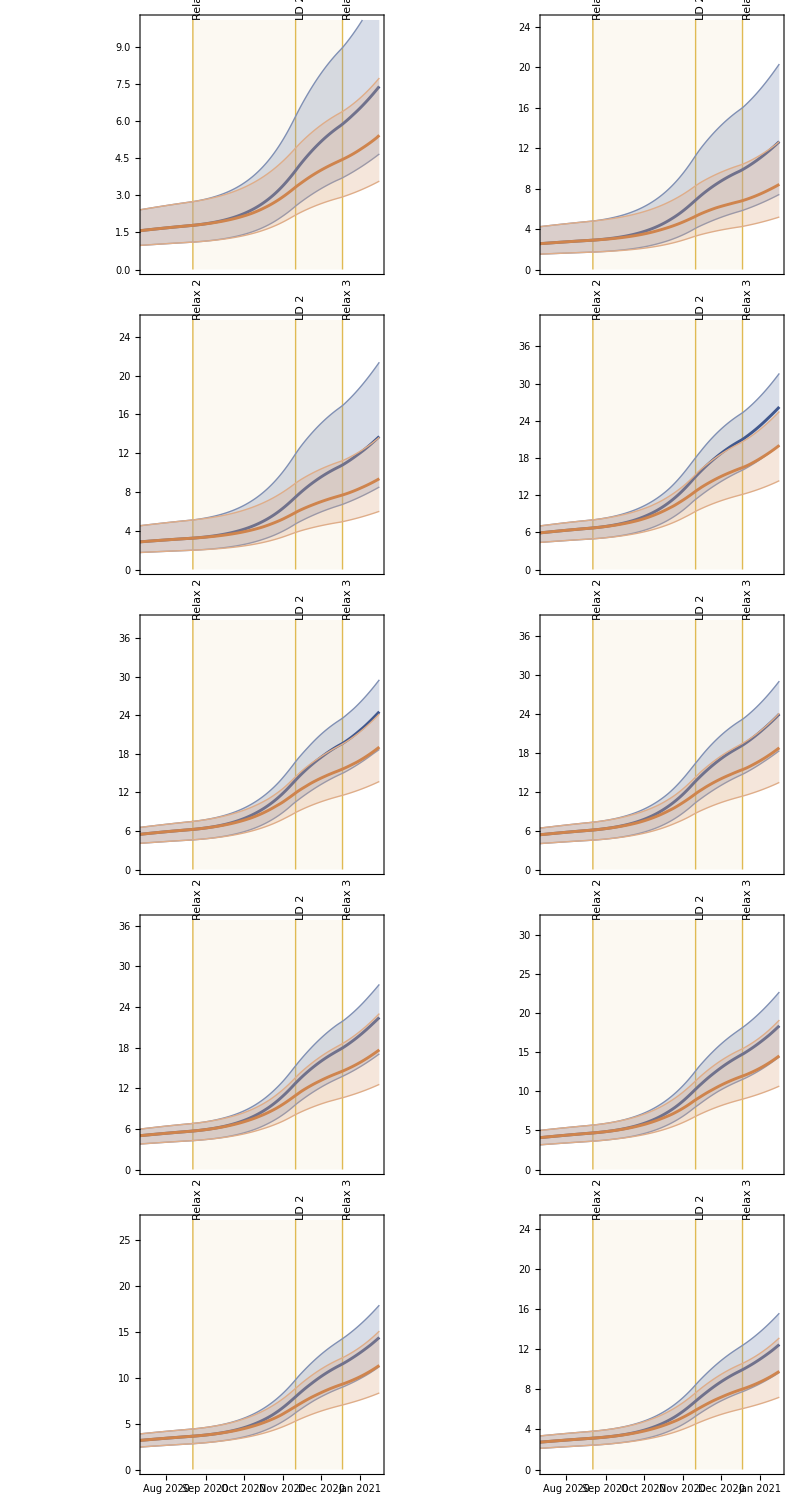
Seroprevalence (%) | -Graphics-
 | Dates

```mathematica
figSero10Scen2=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[seroprevalenceScenarios[[3, k, All, All]]];
maxRange = maxVal+Max[1,10^Floor[Log10[Abs[maxVal]]]];
plotWithLetter[{plotLineWithCrI[seroprevalenceScenarios[[1, k, All, All]],colorBlue,"","","",2,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[seroprevalenceScenarios[[3, k, All, All]],colorOrange]},ageLabelShort[[k]],"left", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figSero10Scen2 = Grid[{{Style[Rotate["Seroprevalence (%)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figSero10Scen2, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figSero10Scen2]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/SEROPREVALENCE_10_SCEN2",  exportFormat[[i]]],figSero10Scen2], {i, 1, Length[exportFormat]}]];
```

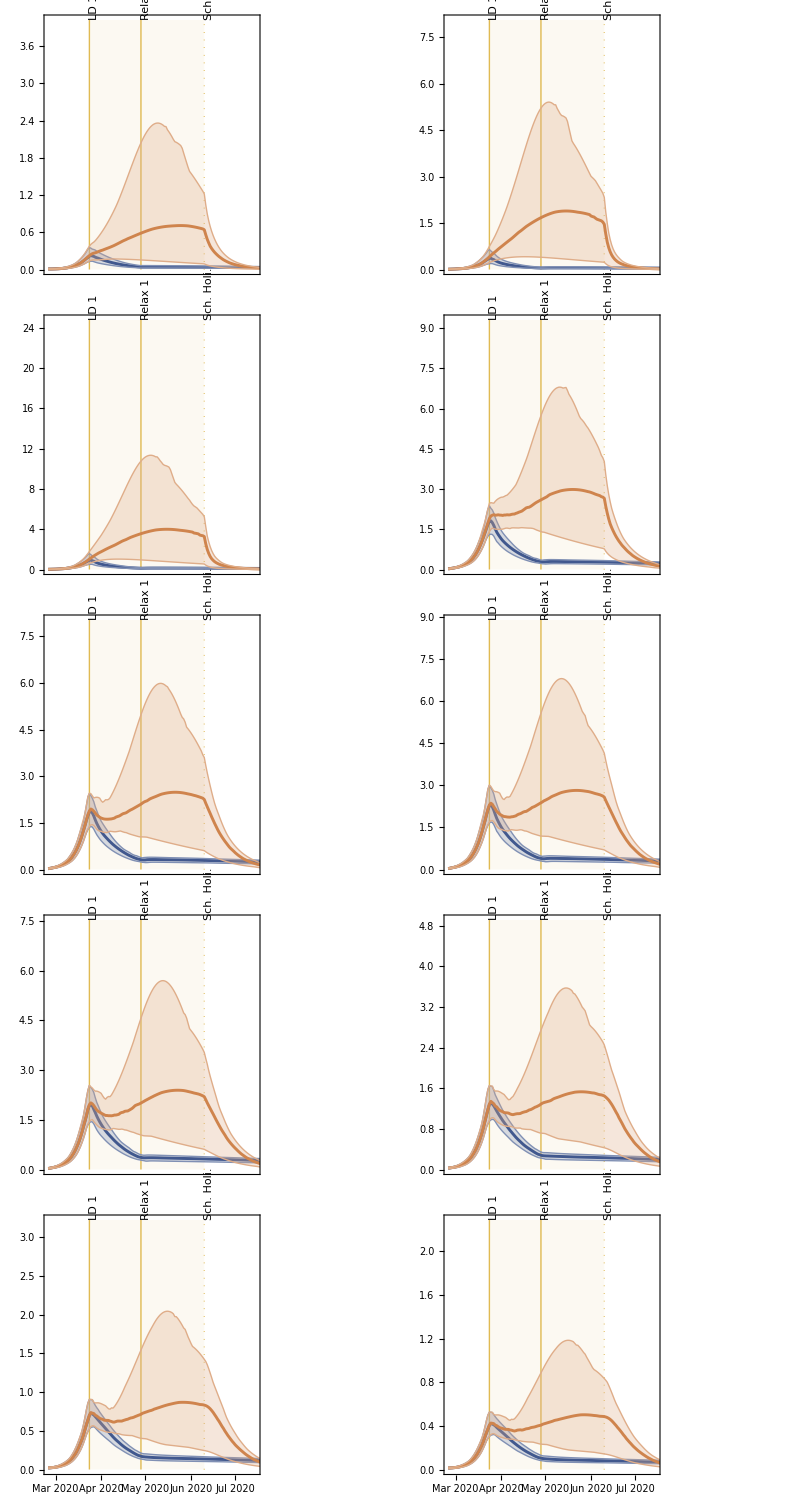
Incidences (1000 people/day) | -Graphics-
 | Dates

```mathematica
figInf10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[incidencesScenarios[[2, k, All, All]]/1000];
maxRange = maxVal+Max[1,10^Floor[Log10[Abs[maxVal]]]];
plotWithLetter[{plotLineWithCrI[incidencesScenarios[[1, k, All, All]]/1000,colorBlue,"","","",1,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[incidencesScenarios[[2, k, All, All]]/1000,colorOrange]},ageLabelShort[[k]],"right", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figInf10Scen1 = Grid[{{Style[Rotate["Incidences (1000 people/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figInf10Scen1, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figInf10Scen1]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/INCIDENCES_10_SCEN1",  exportFormat[[i]]],figInf10Scen1], {i, 1, Length[exportFormat]}]];
```

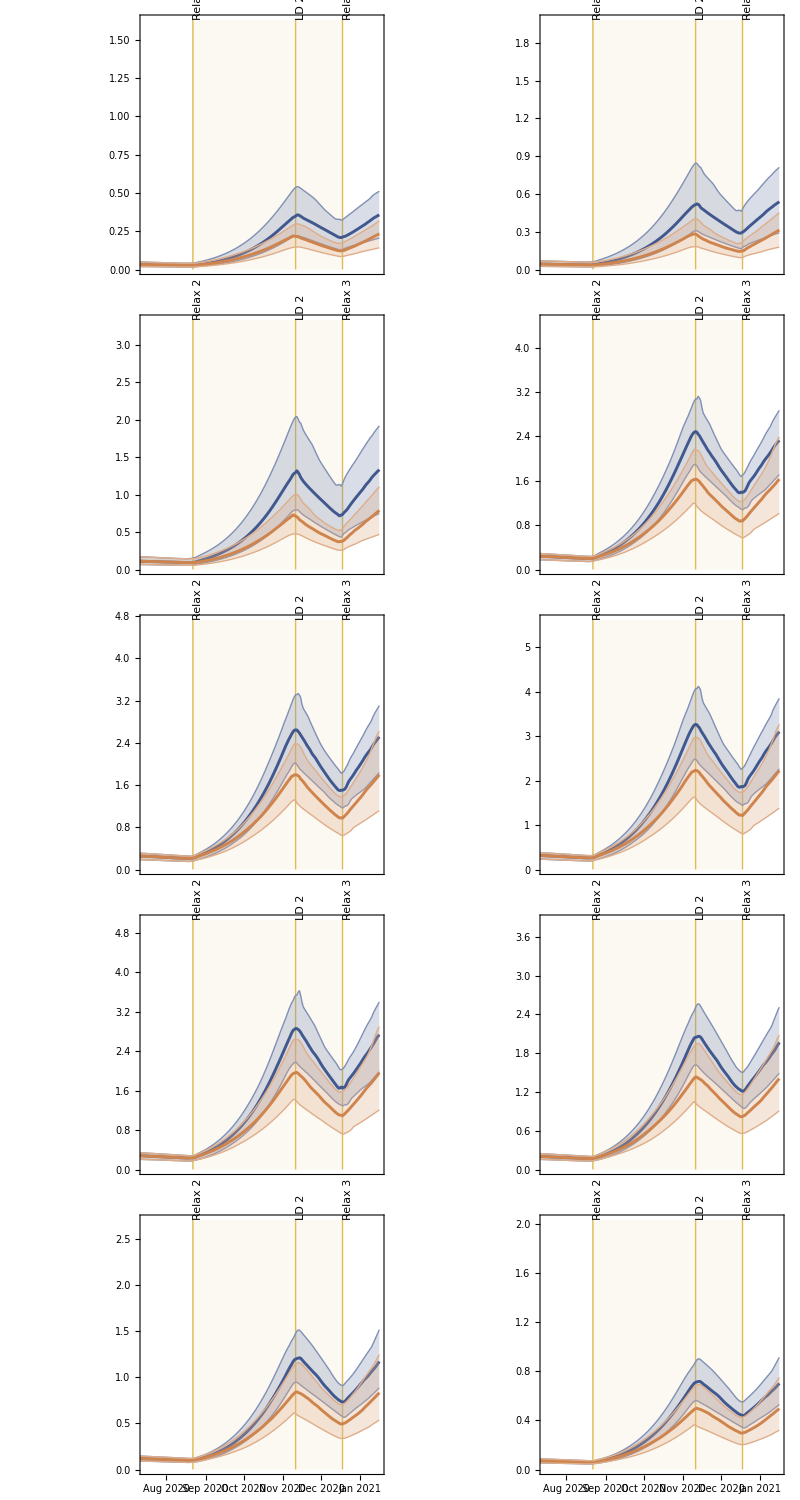
Incidences (1000 people/day) | -Graphics-
 | Dates

```mathematica
figInf10Scen2=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[incidencesScenarios[[1, k, All, All]]/1000];
maxRange = maxVal+Max[1,10^Floor[Log10[Abs[maxVal]]]];
plotWithLetter[{plotLineWithCrI[incidencesScenarios[[1, k, All, All]]/1000,colorBlue,"","","",2,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[incidencesScenarios[[3, k, All, All]]/1000,colorOrange]},ageLabelShort[[k]],"left", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figInf10Scen2 = Grid[{{Style[Rotate["Incidences (1000 people/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figInf10Scen2, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figInf10Scen2]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/INCIDENCES_10_SCEN2",  exportFormat[[i]]],figInf10Scen2], {i, 1, Length[exportFormat]}]];
```

```mathematica
Dimensions[averageContactsTotalScenarios]
```

{3,100,327,10}

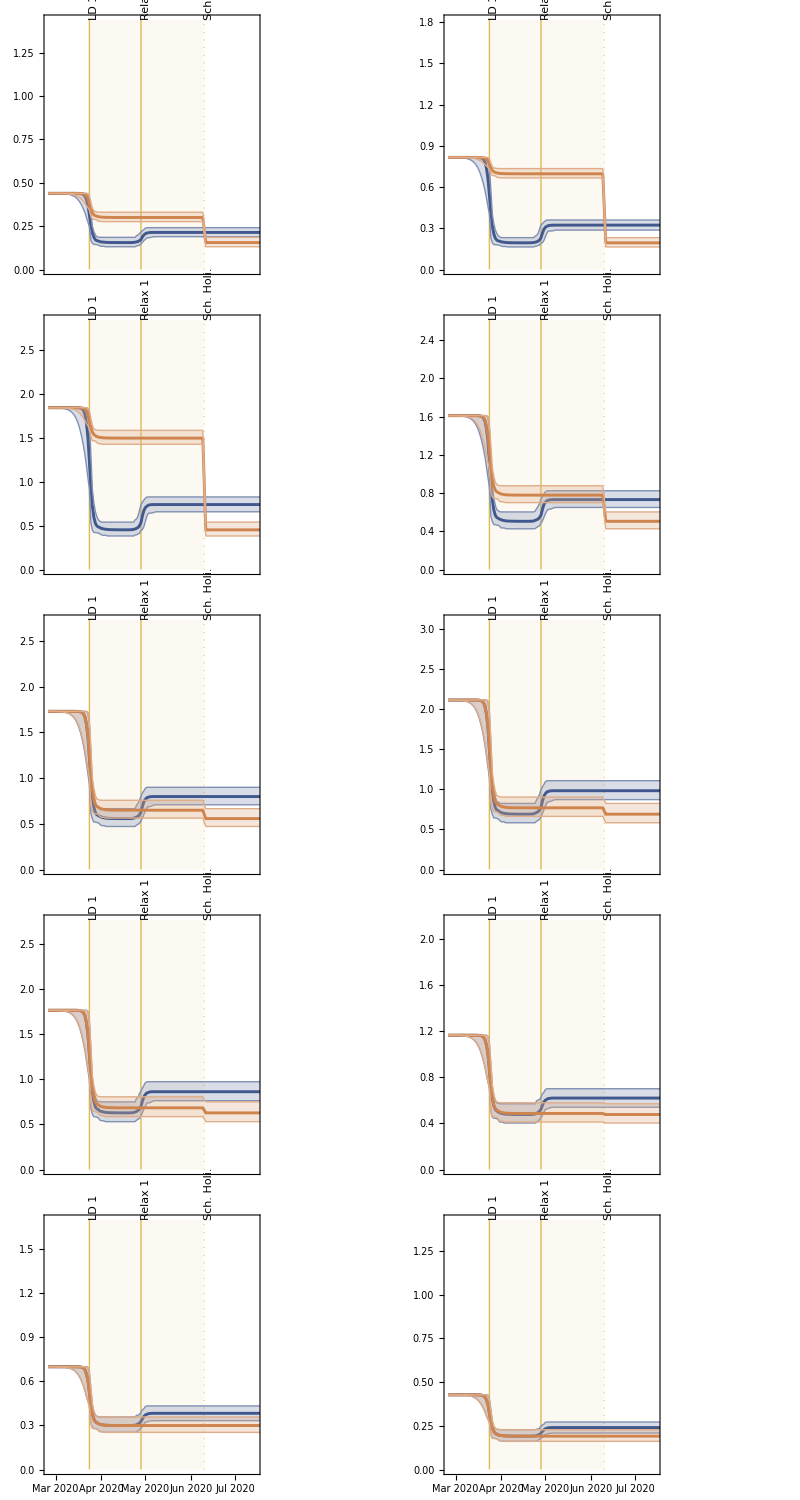
Average contacts (1/day) | -Graphics-
 | Dates

```mathematica
figContacts10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[averageContactsTotalScenarios[[2, All, All, k]]];
maxRange = maxVal+Max[1,10^Floor[Log10[Abs[maxVal]]]];
plotWithLetter[{plotLineWithCrI[averageContactsTotalScenarios[[1, All, All, k]],colorBlue,"","","",1,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[averageContactsTotalScenarios[[2, All, All, k]],colorOrange]},ageLabelShort[[k]],"right", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figContacts10Scen1 = Grid[{{Style[Rotate["Average contacts (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figContacts10Scen1, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figContacts10Scen1]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CONTACTS_AVERAGE_10_SCEN1",  exportFormat[[i]]],figContacts10Scen1], {i, 1, Length[exportFormat]}]];
```

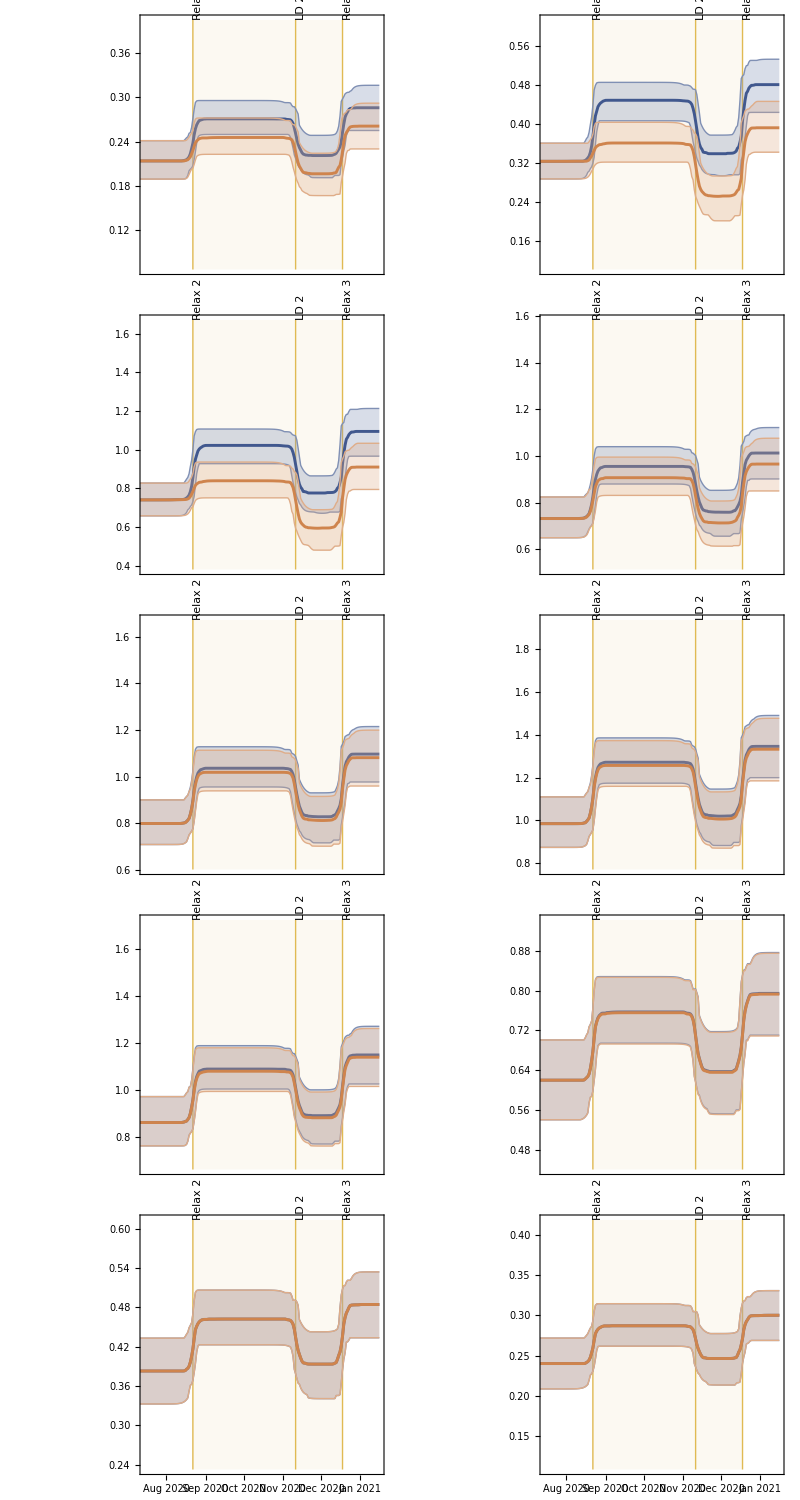
Average contacts (1/day) | -Graphics-
 | Dates

```mathematica
figContacts10Scen2=Table[
Module[{maxVal,minVal, minRange, maxRange}, 
maxVal = Max[Quantile[averageContactsTotalScenarios[[1, All, Range[150, 300], k]], 0.975]];
minVal = Min[Quantile[averageContactsTotalScenarios[[3, All, Range[150, 300], k]], 0.025]];
maxRange = maxVal+Min[0.5,10^Floor[Log10[Abs[maxVal]]]];
minRange = minVal-Min[0.5,10^Floor[Log10[Abs[minVal]]]];
plotWithLetter[{plotLineWithCrI[averageContactsTotalScenarios[[1, All, All, k]],colorBlue,"","","",2,If[k>8,ticksss, None],{minRange, maxRange}, 0.5, 350],
plotLineWithCrI[averageContactsTotalScenarios[[3, All, All, k]],colorOrange]},ageLabelShort[[k]],"left", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figContacts10Scen2 = Grid[{{Style[Rotate["Average contacts (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figContacts10Scen2, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figContacts10Scen2]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CONTACTS_AVERAGE_10_SCEN2",  exportFormat[[i]]],figContacts10Scen2], {i, 1, Length[exportFormat]}]];
```

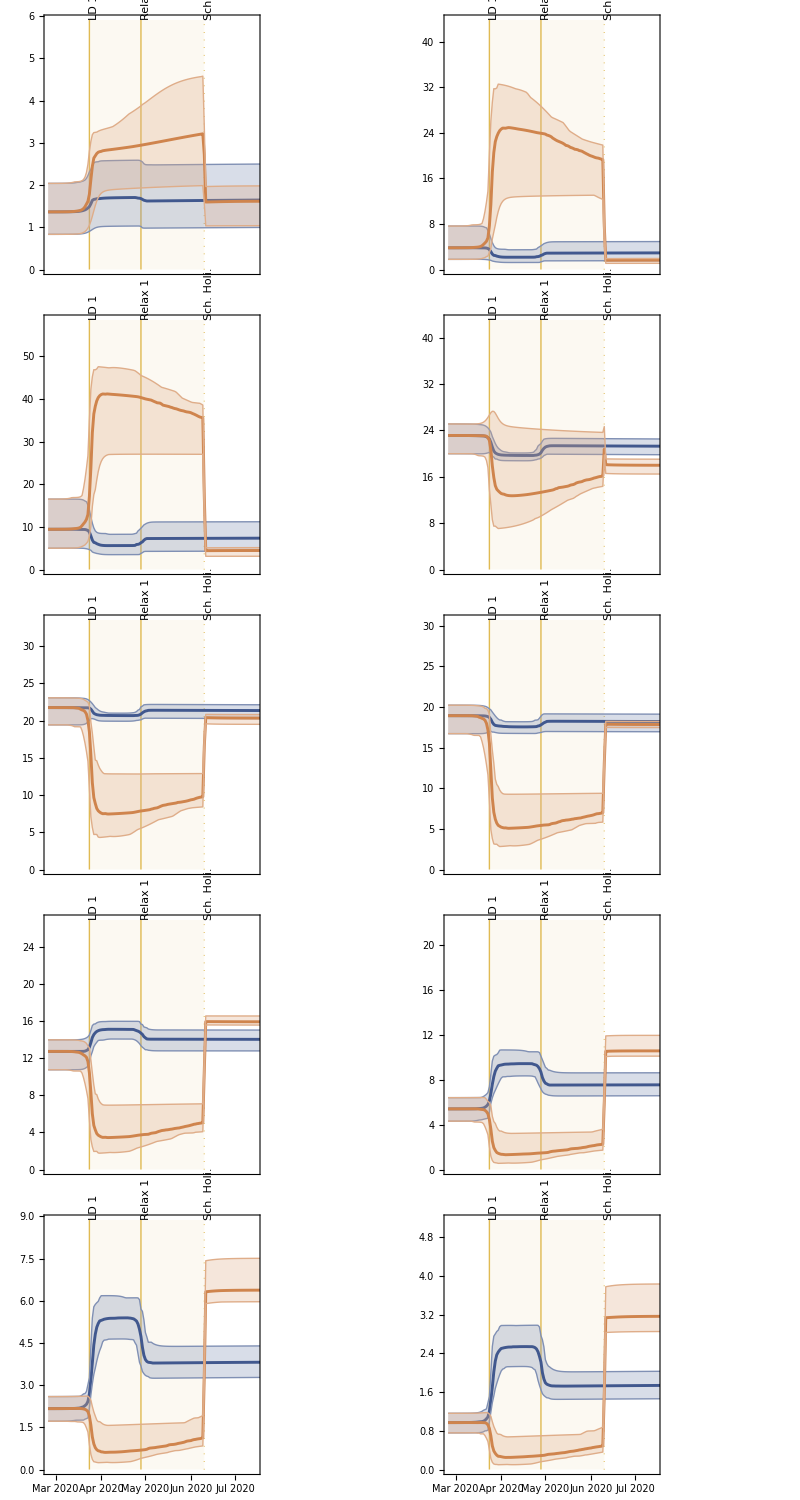
Cumulative elasticities (%) | -Graphics-
 | Dates

```mathematica
figCumuElas10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Max[100cumuElasScenarios[[2, All, All, k]]];
maxRange = maxVal+Max[1,10^Floor[Log10[Abs[maxVal]]]];
plotWithLetter[{plotLineWithCrI[100cumuElasScenarios[[1, All, All, k]],colorBlue,"","","",1,If[k>8,ticksss, None],{0, maxRange}, 0.5, 350],
plotLineWithCrI[100cumuElasScenarios[[2, All, All, k]],colorOrange]},ageLabelShort[[k]],"right", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figCumuElas10Scen1 = Grid[{{Style[Rotate["Cumulative elasticities (%)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figCumuElas10Scen1, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figCumuElas10Scen1]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CUMU_ELAS_10_SCEN1",  exportFormat[[i]]],figCumuElas10Scen1], {i, 1, Length[exportFormat]}]];
```

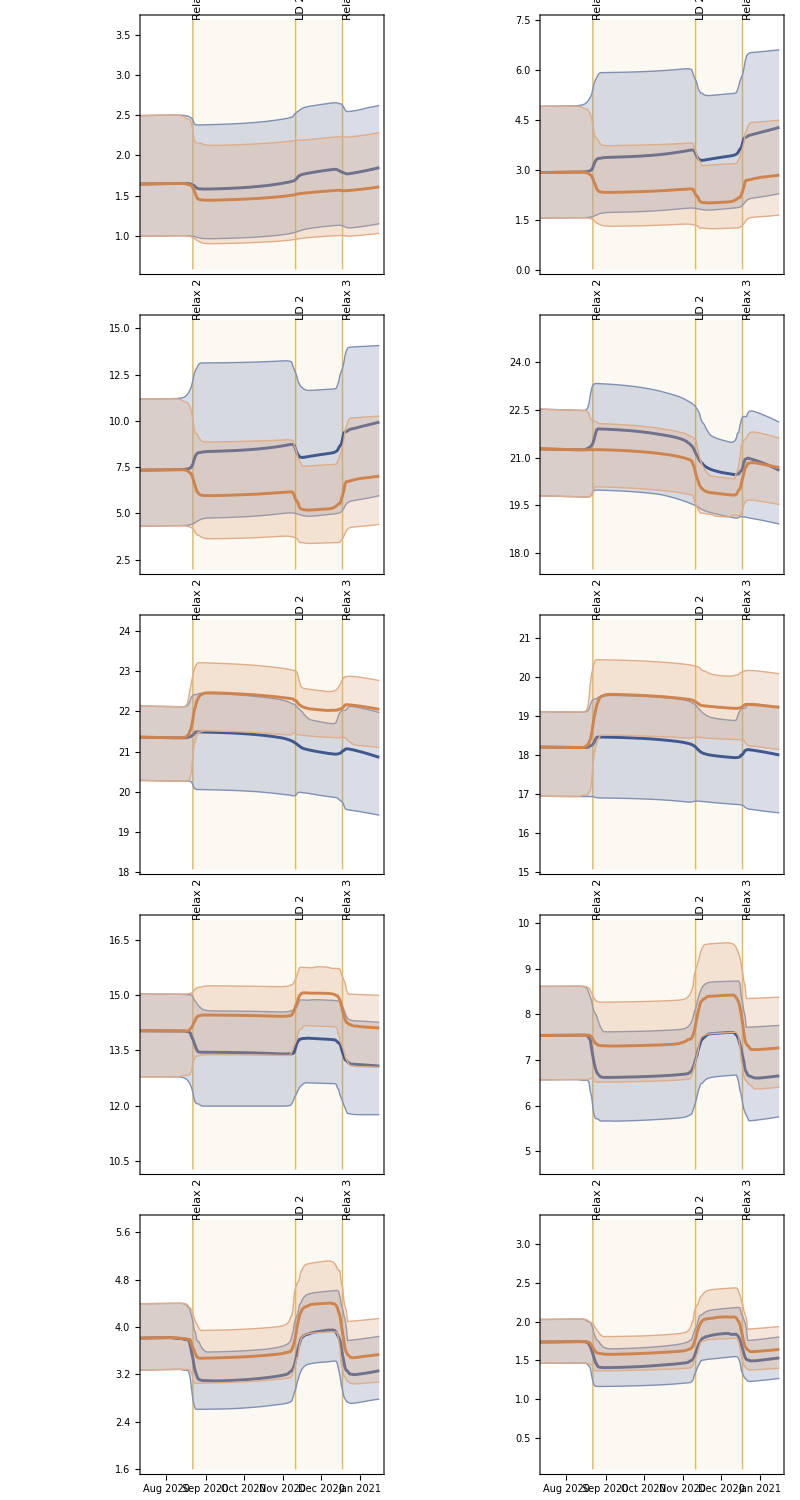
Cumulative elasticities (%) | -Graphics-
 | Dates

```mathematica
figCumuElas10Scen2=Table[
Module[{maxVal,minVal,minRange, maxRange}, 
maxVal = Max[100cumuElasScenarios[[1,All, Range[150,300], k]]];
minVal = Min[100cumuElasScenarios[[1, All,Range[150,300], k]]];
maxRange = maxVal+Min[1.5,10^Floor[Log10[Abs[maxVal]]]];
minRange = minVal-Min[1.5,10^Floor[Log10[Abs[minVal]]]];
plotWithLetter[{plotLineWithCrI[100cumuElasScenarios[[1, All, All, k]],colorBlue,"","","",2,If[k>8,ticksss, None],{minRange, maxRange}, 0.5, 350],
plotLineWithCrI[100cumuElasScenarios[[3, All, All, k]],colorOrange]},ageLabelShort[[k]],"left", sizeFontBig, colorDarkRainbow4AgeGroups[[k]]]], {k, 1, numAgeGroups}];
figCumuElas10Scen2 = Grid[{{Style[Rotate["Cumulative elasticities (%)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figCumuElas10Scen2, {5,2}]]}, {"", Style["Dates",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figCumuElas10Scen2]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/CUMU_ELAS_10_SCEN2",  exportFormat[[i]]],figCumuElas10Scen2], {i, 1, Length[exportFormat]}]];
```

```mathematica
sensMatMedian = Median[Transpose[Re[sensScenarios]]];
sensMatLower= Quantile[Transpose[Re[sensScenarios]], 0.025];
sensMatUpper = Quantile[Transpose[Re[sensScenarios]], 0.975];
scen1SensTitles = Flatten[{"Before LD1", diagramLabelsShort[[1;;2]], "School holidays"}];
scen2SensTitles = diagramLabelsShort[[2;;5]];
```

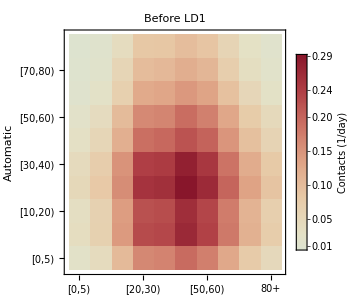
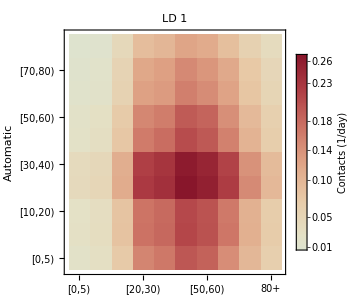
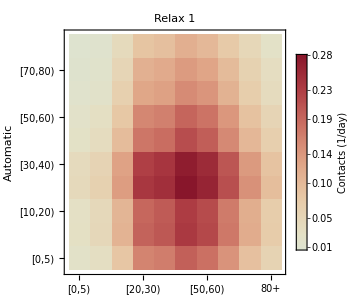
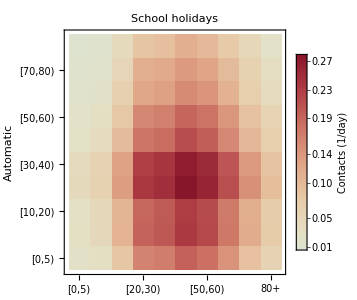
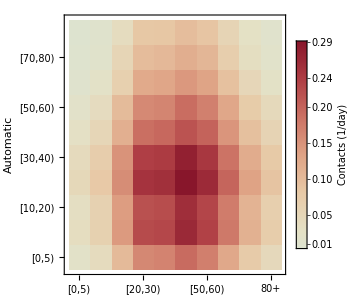
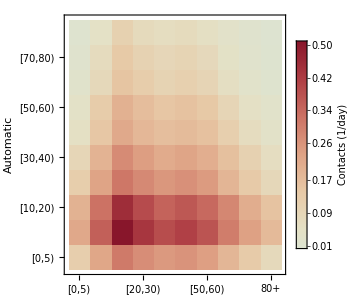
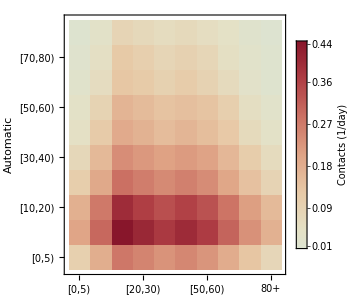
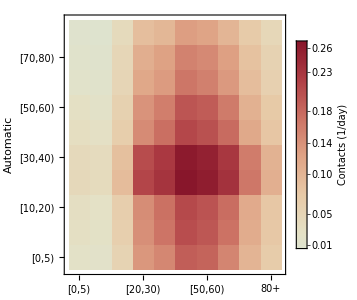
Age of infectee (years) | Baseline | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Scenario 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Age of infector (years)

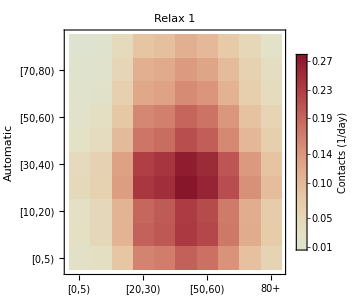
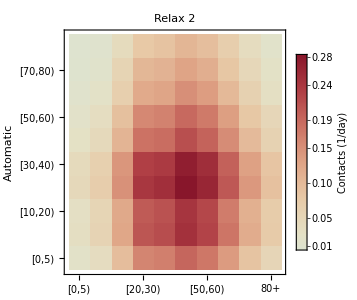
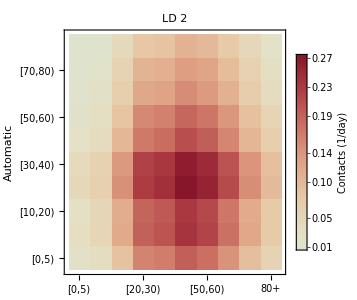
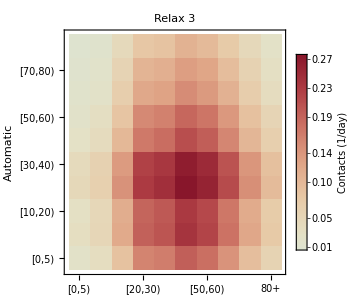
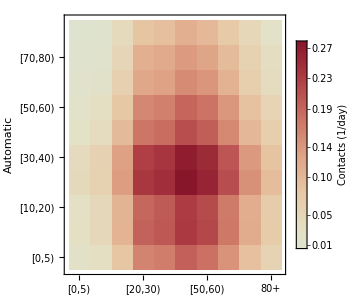
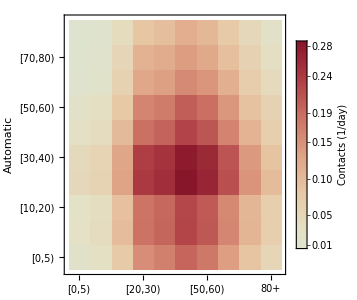
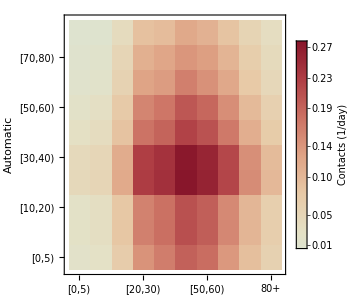
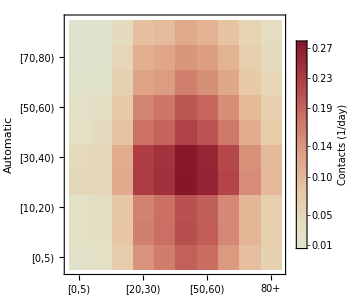
Age of infectee (years) | Baseline | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Scenario 2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Age of infector (years)

```mathematica
(*Remove["plottingFunctions`*"]
Get["../packages/plottingFunctions.m"]
*)
figSensScen1= Table[Table[plotMatrix[sensMatMedian[[j,scen1Differences[[i]]]], "ThermometerColors",
 If[j === 1,scen1SensTitles[[i]], ""], True], {i, 1, Length[scen1Differences]}], {j, {1, 2}}];
figSensScen2= Table[Table[plotMatrix[sensMatMedian[[j,scen2Differences[[i]]]], "ThermometerColors",
 If[j === 1,scen2SensTitles[[i]], ""], True], {i, 1, Length[scen2Differences]}], {j, {1, 3}}];


figSensScenario1 = Grid[{{Style[Rotate["Age of infectee (years)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],
Grid[{Flatten[{
Style[Rotate["Baseline", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figSensScen1[[1]]}], Flatten[{Style[Rotate["Scenario 1", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figSensScen1[[2]]}]}]}, {"",Style["Age of infector (years)",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figSensScenario1]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/SENSITIVITY_10_SCEN1",  exportFormat[[i]]],figSensScenario1], {i, 1, Length[exportFormat]}]];

figSensScenario2 = Grid[{{Style[Rotate["Age of infectee (years)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],
Grid[{Flatten[{
Style[Rotate["Baseline", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figSensScen2[[1]]}], Flatten[{Style[Rotate["Scenario 2", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figSensScen2[[2]]}]}]}, {"",Style["Age of infector (years)",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, figSensScenario2]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/SENSITIVITY_10_SCEN2",  exportFormat[[i]]],figSensScenario2], {i, 1, Length[exportFormat]}]];
```

```mathematica
sumRanges[matrix_]:=Module[{rows,cols,result},rows={Total[matrix[[1;;3,All]]],Total[matrix[[4;;10,All]]]}//Map[Total];
cols={Total[matrix[[All,1;;3]]],Total[matrix[[All,4;;10]]]}//Map[Total];
result={{rows[[1]],cols[[1]]},{rows[[2]],cols[[2]]}};
Transpose[result]];
twoSensScenarios = ConstantArray[0,{numScenarios,numSamples,numTimes,2,2}];
Do[twoSensScenarios[[i,j,k, All,All]]=sumRanges[sensScenarios[[i,j,k, All,All]]];,{i,1,numScenarios},{j,1,numSamples},{k,1,numTimes}];
```

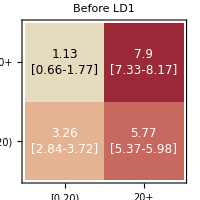
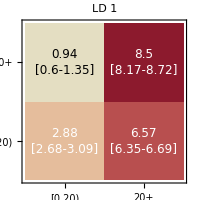
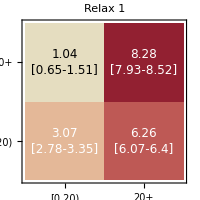
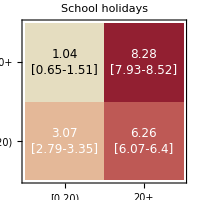
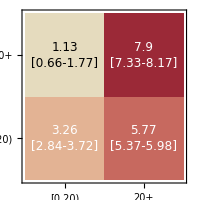
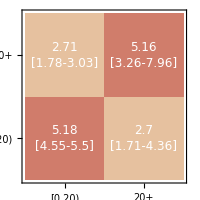
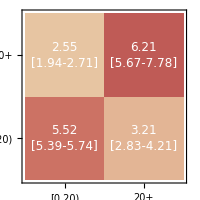
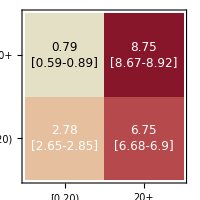
Age of participant (years) | Baseline | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Scenario 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Age of contact (years)

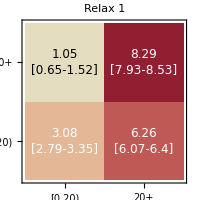
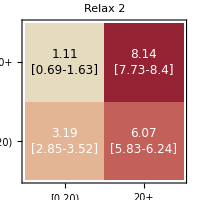
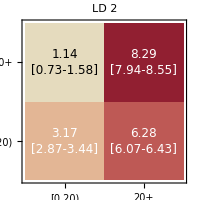
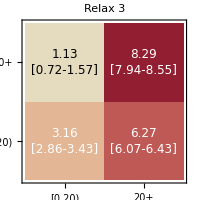
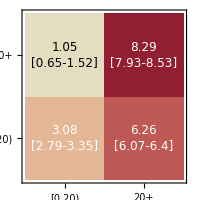
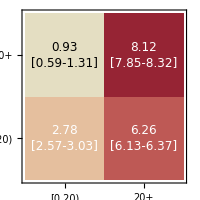
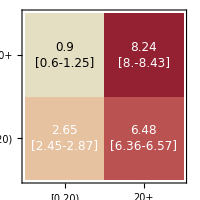
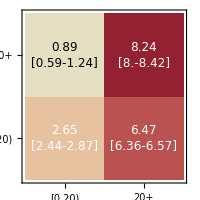
Age of participant (years) | Baseline | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Scenario 2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Age of contact (years)

```mathematica
twoSensMedian = Median[Transpose[Re[twoSensScenarios]]];
twoSensLower= Quantile[Transpose[Re[twoSensScenarios]], 0.025];
twoSensUpper = Quantile[Transpose[Re[twoSensScenarios]], 0.975];

figTwoSensScen1= Table[Table[plotMatrix2[twoSensMedian[[j,scen1Differences[[i]]]],
twoSensLower[[j,scen1Differences[[i]]]],
twoSensUpper[[j,scen1Differences[[i]]]],
If[j === 1,scen1CMTitles[[i]], ""],False], {i, 1, Length[scen1Differences]}], {j, {1, 2}}];
figTwoSensScen2= Table[Table[plotMatrix2[twoSensMedian[[j,scen2Differences[[i]]]],
twoSensLower[[j,scen2Differences[[i]]]],
twoSensUpper[[j,scen2Differences[[i]]]],
If[j === 1,scen2CMTitles[[i]], ""],False], {i, 1, Length[scen2Differences]}], {j, {1, 3}}];

fig2SensScenario1 = Grid[{{Style[Rotate["Age of participant (years)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],
Grid[{Flatten[{
Style[Rotate["Baseline", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figTwoSensScen1[[1]]}], Flatten[{Style[Rotate["Scenario 1", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figTwoSensScen1[[2]]}]}]}, {"",Style["Age of contact (years)",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, fig2SensScenario1]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/SENSITIVITY_2_SCEN1",  exportFormat[[i]]],fig2SensScenario1], {i, 1, Length[exportFormat]}]];

fig2SensScenario2 = Grid[{{Style[Rotate["Age of participant (years)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],
Grid[{Flatten[{
Style[Rotate["Baseline", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figTwoSensScen2[[1]]}], Flatten[{Style[Rotate["Scenario 2", Pi/2],Black,sizeFontBig,Bold, FontFamily->"Helvetica"],figTwoSensScen2[[2]]}]}]}, {"",Style["Age of contact (years)",Black,sizeFontBig, FontFamily->"Helvetica"]}}];
If[ifShowFigs, fig2SensScenario2]
If[ifExportFigs, 
Table[Export[StringJoin["../figures/SENSITIVITY_2_SCEN2",  exportFormat[[i]]],fig2SensScenario2], {i, 1, Length[exportFormat]}]];
```

## Extra figures for scenario-centric plots

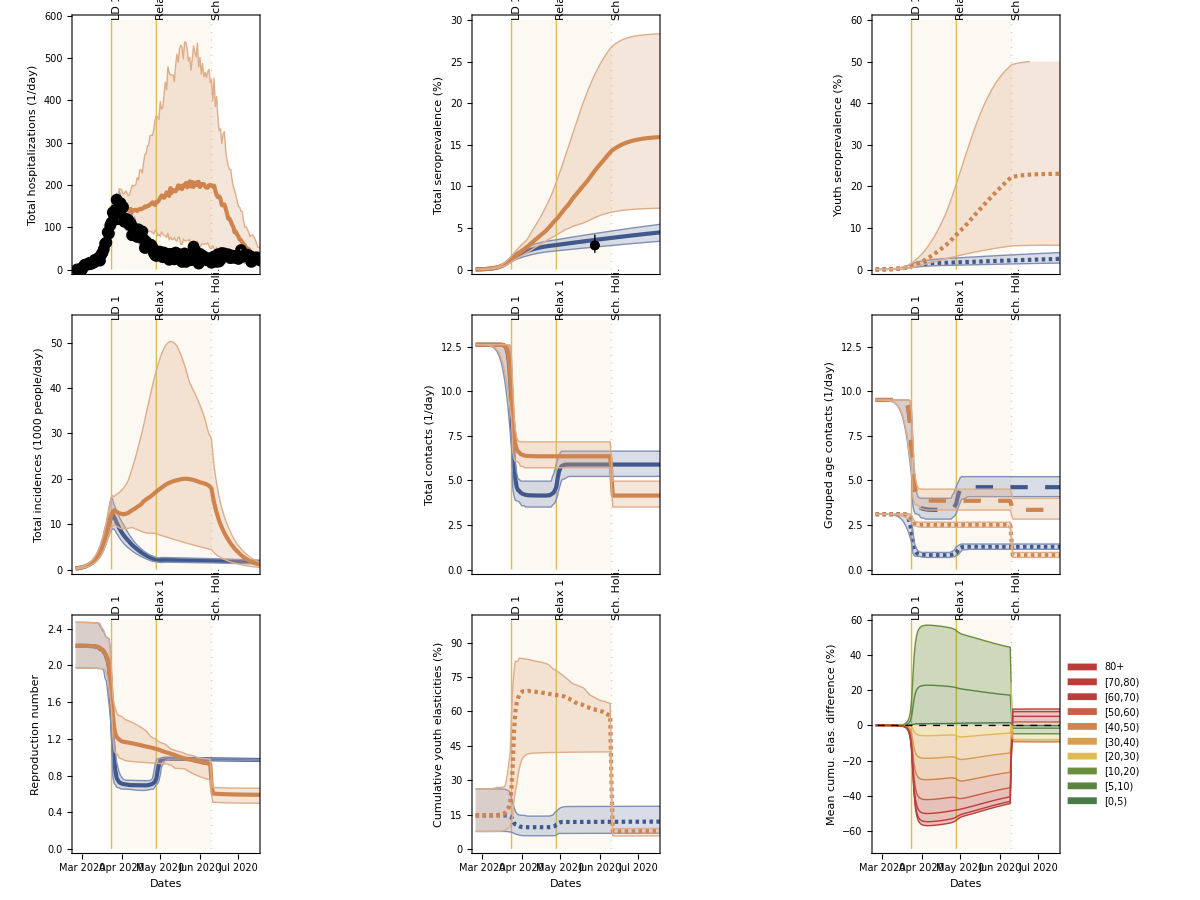
Scenario 1: Schools open during the first lockdown
-Graphics-

{../figures/ALL_SCENARIO_1.pdf,../figures/ALL_SCENARIO_1.eps}

```mathematica
figHospTotal1 = plotWithLetter[{plotLineWithCrI[hospitalizationSimulatedScenariosTotal[[1,1, All, All]],colorBlue,"","","Total hospitalizations (1/day)",1,None,{0,590}],plotLineWithCrI[hospitalizationSimulatedScenariosTotal[[2,1, All, All]],colorOrange],scatterPlotHospData},"A","right"];
figSeroTotal1 = plotWithLetter[{plotLineWithCrI[seroprevalenceScenariosTotal[[1,1, All, All]],colorBlue,"","","Total seroprevalence (%)",1,None,{0,30}],plotLineWithCrI[seroprevalenceScenariosTotal[[2,1, All, All]],colorOrange],scatterPlotSeroSinglePoint},"B","right"];
figSeroYouth1 = plotWithLetter[{plotLineWithCrI[seroprevalenceScenariosGrouped[[1,1, All, All]],colorBlue,"","","Youth seroprevalence (%)",1,None,{0,60}, 0.5, 500,Dashing[{0.005, 0.005}] ],plotLineWithCrI[seroprevalenceScenariosGrouped[[2,1, All, All]],colorOrange,"","","Youth seroprevalence (%)",1,None,{0,50}, 0.5, 500,Dashing[{0.005, 0.005}]]},"C","right"];
(*figSeroYouth1 = Legended[figSeroYouth1, LineLegend[{colorBlue, colorOrange}, {"baseline", "scenario"}]];
*)

figIncidTotal1 = plotWithLetter[{plotLineWithCrI[incidencesScenariosTotal[[1,1, All, All]]/1000,colorBlue,"","","Total incidences (1000 people/day)",1,None,{0,55}],plotLineWithCrI[incidencesScenariosTotal[[2,1, All, All]]/1000,colorOrange]},"D","right"];
figAverageContactsTotalScen1 = plotWithLetter[{plotLineWithCrI[averageContactsTotal[[1,All,All]],colorBlue,"","","Total contacts (1/day)",1,None,{0, 14}, 0.5, 500],plotLineWithCrI[averageContactsTotal[[2,All,All]],colorOrange,"","","",1,None,{0, 14}, 0.5, 500]},"E","right"];
figAverageContactsGroupedScen1 = plotWithLetter[{plotLineWithCrI[averageContactsAdults[[1,All,All]],colorBlue,"","","Grouped age contacts (1/day)",1,None,{0, 14}, 0.5, 500, Dashing[{0.025, 0.025}]],plotLineWithCrI[averageContactsAdults[[2,All,All]],colorOrange,"","","",1,None,{0, 14}, 0.5, 500, Dashing[{0.025, 0.025}]],
plotLineWithCrI[averageContactsYouth[[1,All,All]],colorBlue,"","","",1,None,{0, 14}, 0.5, 500, Dashing[{0.005, 0.005}]],plotLineWithCrI[averageContactsYouth[[2,All,All]],colorOrange,
"","","",1,None,{0, 14}, 0.5, 500, Dashing[{0.005, 0.005}]]},"F","right", sizeFontBigger, Black, legendGroupedAgesScen1];
(*figAverageContactsGroupedScen1 = Legended[figAverageContactsGroupedScen1, LineLegend[{Solid ,Dashing[{0.025, 0.025}], Dashing[{0.005, 0.005}]}, {"total", "adults, 20+", "youth, 0-20"}]];*)

figRt1 = plotWithLetter[{plotLineWithCrI[RtScenarios[[1,All,All,1]],colorBlue,"","Dates","Reproduction number",1,ticksss,{0,2.5}],plotLineWithCrI[RtScenarios[[2,All,All,1]],colorOrange]},"G","right"];
figYouthCumuElas1 = plotWithLetter[{plotLineWithCrI[100cumuElasGroupedScenarios[[1,All,All,1]],colorBlue,"","Dates","Cumulative youth elasticities (%)",1,ticksss,{0,100}, 0.5, 500,Dashing[{0.005, 0.005}] ],
plotLineWithCrI[100cumuElasGroupedScenarios[[2,All,All,1]],colorOrange,"","","Cumulative youth elasticities (%)",1,ticksss,{0,100}, 0.5, 500,Dashing[{0.005, 0.005}] ]},"H","right"];
figCumuElasMean1Diff = plotWithLetter[plotStackedLinesMoving[100cumuElasDiffScenariosMeanScen1, 1, True, {-70,60}, "Mean cumu. elas. difference (%)"], "I", "right"];

figScenario1 = Grid[{{Style["Scenario 1: Schools open during the first lockdown",Black,Bold, sizeFontBig, FontFamily->"Helvetica"]}, {Grid[{{figHospTotal1, figSeroTotal1, figSeroYouth1},
{figIncidTotal1, figAverageContactsTotalScen1, figAverageContactsGroupedScen1},
{figRt1,figYouthCumuElas1,figCumuElasMean1Diff}}]}}];
If[ifShowFigs, figScenario1]
Table[Export[StringJoin["../figures/ALL_SCENARIO_1",  exportFormat[[i]]],figScenario1], {i, 1, Length[exportFormat]}]
(*If[ifExportFigs, 
Table[Export[StringJoin["../figures/ALL_SCENARIO_1",  exportFormat[[i]]],figScenario1], {i, 1, Length[exportFormat]}]];*)
```

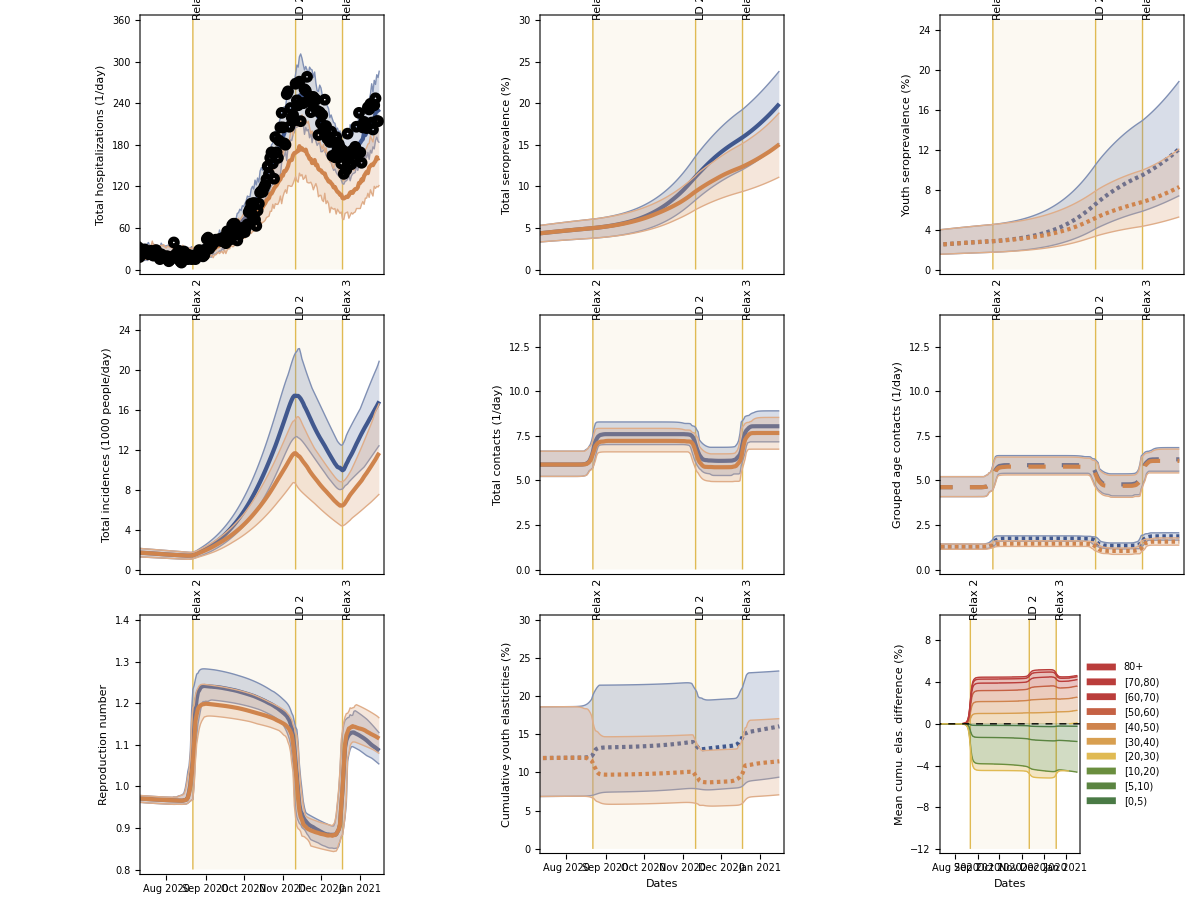
Scenario 2: Schools closed after the summer holiday
-Graphics-

```mathematica
figHospTotal2 = plotWithLetter[{plotLineWithCrI[hospitalizationSimulatedScenariosTotal[[1,1, All, All]],colorBlue,"","","Total hospitalizations (1/day)",2,None,{0,360}],plotLineWithCrI[hospitalizationSimulatedScenariosTotal[[3,1, All, All]],colorOrange],scatterPlotHospData},"A","right"];
figSeroTotal2 = plotWithLetter[{plotLineWithCrI[seroprevalenceScenariosTotal[[1,1, All, All]],colorBlue,"","","Total seroprevalence (%)",2,None,{0,30}],plotLineWithCrI[seroprevalenceScenariosTotal[[3,1, All, All]],colorOrange],scatterPlotSeroSinglePoint},"B","right"];
figSeroYouth2 = plotWithLetter[{plotLineWithCrI[seroprevalenceScenariosGrouped[[1,1, All, All]],colorBlue,"","","Youth seroprevalence (%)",2,None,{0,25}, 0.5, 500,Dashing[{0.005, 0.005}] ],plotLineWithCrI[seroprevalenceScenariosGrouped[[3,1, All, All]],colorOrange,"","","Youth seroprevalence (%)",2,None,{0,25}, 0.5, 500,Dashing[{0.005, 0.005}]]},"C","right"];
(*figSeroYouth1 = Legended[figSeroYouth1, LineLegend[{colorBlue, colorOrange}, {"baseline", "scenario"}]];
*)

figIncidTotal2 = plotWithLetter[{plotLineWithCrI[incidencesScenariosTotal[[1,1, All, All]]/1000,colorBlue,"","","Total incidences (1000 people/day)",2,None,{0,25}],plotLineWithCrI[incidencesScenariosTotal[[3,1, All, All]]/1000,colorOrange]},"D","right"];
figAverageContactsTotalScen2 = plotWithLetter[{plotLineWithCrI[averageContactsTotal[[1,All,All]],colorBlue,"","","Total contacts (1/day)",2,None,{0, 14}, 0.5, 500],plotLineWithCrI[averageContactsTotal[[3,All,All]],colorOrange,"","","",2,None,{0, 14}, 0.5, 500]},"E","right"];
figAverageContactsGroupedScen2 = plotWithLetter[{plotLineWithCrI[averageContactsAdults[[1,All,All]],colorBlue,"","","Grouped age contacts (1/day)",2,None,{0, 14}, 0.5, 500, Dashing[{0.025, 0.025}]],plotLineWithCrI[averageContactsAdults[[3,All,All]],colorOrange,"","","",2,None,{0, 14}, 0.5, 500, Dashing[{0.025, 0.025}]],
plotLineWithCrI[averageContactsYouth[[1,All,All]],colorBlue,"","","",2,None,{0, 14}, 0.5, 500, Dashing[{0.005, 0.005}]],plotLineWithCrI[averageContactsYouth[[3,All,All]],colorOrange,
"","","",2,None,{0, 14}, 0.5, 500, Dashing[{0.005, 0.005}]]},"F","right", sizeFontBigger, Black, legendGroupedAgesScen2];
(*figAverageContactsGroupedScen1 = Legended[figAverageContactsGroupedScen1, LineLegend[{Solid ,Dashing[{0.025, 0.025}], Dashing[{0.005, 0.005}]}, {"total", "adults, 20+", "youth, 0-20"}]];*)

figRt2 = plotWithLetter[{plotLineWithCrI[RtScenarios[[1,All,All,1]],colorBlue,"","","Reproduction number",2,ticksss,{0.8,1.4}],plotLineWithCrI[RtScenarios[[3,All,All,1]],colorOrange]},"G","right"];
figYouthCumuElas2 = plotWithLetter[{plotLineWithCrI[100cumuElasGroupedScenarios[[1,All,All,1]],colorBlue,"","Dates","Cumulative youth elasticities (%)",2,ticksss,{0,30}, 0.5, 500,Dashing[{0.005, 0.005}] ],
plotLineWithCrI[100cumuElasGroupedScenarios[[3,All,All,1]],colorOrange,"","Dates","Cumulative youth elasticities (%)",2,ticksss,{0,30}, 0.5, 500,Dashing[{0.005, 0.005}] ]},"H","right"];
figCumuElasMean2Diff = plotWithLetter[plotStackedLinesMoving[100cumuElasDiffScenariosMeanScen2, 2, True, {-12,10}, "Mean cumu. elas. difference (%)"], "I", "right"];

figScenario2 = Grid[{{Style["Scenario 2: Schools closed after the summer holiday",Black,Bold, sizeFontBig, FontFamily->"Helvetica"]}, {Grid[{{figHospTotal2, figSeroTotal2, figSeroYouth2},
{figIncidTotal2, figAverageContactsTotalScen2, figAverageContactsGroupedScen2},
{figRt2,figYouthCumuElas2,figCumuElasMean2Diff}}]}}];
If[ifShowFigs, figScenario2]
Table[Export[StringJoin["../figures/ALL_SCENARIO_2",  exportFormat[[i]]],figScenario2], {i, 1, Length[exportFormat]}];
(*If[ifExportFigs, 
Table[Export[StringJoin["../figures/ALL_SCENARIO_2",  exportFormat[[i]]],figScenario2], {i, 1, Length[exportFormat]}]];*)
```